# Fitting With DNNs

Markus van Almsick, WRI

## Creating Data

```mathematica
originaldata=Import["https://github.com/madsutherland/Project/blob/master/Molecular%20Structures%20Real/Table%20of%20Aouidate%20data.xlsx?raw=true","XLSX"];
```

```mathematica
sheet=originaldata[[1]]
```

(logMU | ET | IP | EHOMO | η | ELUMO | DM | Qp | Qmin | MW | n | γ | D | logP | 
2.72 | −82328.726 | 7.374 | −5.682 | 5.522 | −0.160 | 3.242 | 0.046 | −0.707 | 274.154 | 1.54 | 37.9 | 1.324 | 2.455 | 
1.96 | −30241.000 | 7.125 | −5.428 | 5.258 | −0.170 | 1.996 | 0.135 | −0.708 | 255.376 | 1.545 | 42.6 | 1.08 | 2.452 | 
2.02 | −19406.400 | 6.731 | −5.029 | 5.302 | 0.273 | 1.234 | 0.126 | −0.712 | 223.311 | 1.509 | 33.9 | 0.998 | 2.778 | 
1.95 | −20476.100 | 6.724 | −5.037 | 5.295 | 0.258 | 1.283 | 0.126 | −0.709 | 237.338 | 1.507 | 33.9 | 0.998 | 3.307 | 
1.9 | −18336.700 | 6.765 | −5.009 | 5.282 | 0.273 | 1.117 | 0.127 | −0.710 | 209.285 | 1.511 | 34.2 | 1.01 | 2.249 | 
1.71 | −31310.656 | 7.238 | −4.780 | 5.066 | 0.286 | 2.498 | −0.150 | −0.712 | 269.403 | 1.539 | 41.2 | 1.07 | 2.761 | 
1.69 | −86156.656 | 7.374 | −5.687 | 5.527 | −0.160 | 3.271 | 0.046 | −0.709 | 260.128 | 1.548 | 39.5 | 1.368 | 2.146 | 
1.68 | −21545.885 | 6.721 | −5.025 | 5.3 | 0.275 | 1.25 | 0.122 | −0.713 | 251.365 | 1.504 | 33.9 | 0.979 | 3.386 | 
1.66 | −29171.207 | 7.121 | −5.453 | 5.295 | −0.158 | 2.115 | −0.131 | −0.707 | 241.35 | 1.55 | 43.1 | 1.1 | 1.923 | 
1.36 | −29171.025 | 6.993 | −5.327 | 5.234 | −0.093 | 4.017 | −0.219 | −0.713 | 241.35 | 1.552 | 44.2 | 1.1 | 1.743 | 
1.33 | −20382.821 | 6.83 | −5.101 | 5.576 | 0.475 | 3.159 | 0.349 | −0.713 | 225.284 | 1.507 | 34.3 | 1.048 | 1.392 | 
1.25 | −18336.601 | 6.802 | −5.024 | 5.301 | 0.278 | 1.323 | 0.125 | −0.716 | 209.285 | 1.514 | 34.9 | 1.012 | 2.469 | 
1.29 | −30240.922 | 7.156 | −5.333 | 5.236 | −0.097 | 4.084 | −0.220 | −0.707 | 255.376 | 1.547 | 43.6 | 1.09 | 2.272 | 
1.27 | −17266.813 | 8.353 | −5.142 | 5.451 | 0.309 | 1.618 | 0.133 | −0.714 | 195.258 | 1.516 | 35.3 | 1.026 | 1.94 | 
1.14 | −22396.415 | 7.075 | −5.349 | 5.755 | 0.407 | 1.297 | 0.273 | −0.713 | 239.268 | 1.54 | 43.5 | 1.184 | 1.644 | 
1.36 | −21452.636 | 6.803 | −5.073 | 5.531 | 0.458 | 3.234 | 0.353 | −0.707 | 239.311 | 1.504 | 34.3 | 1.034 | 1.921 | 
1.11 | −28101.400 | 7.292 | −5.423 | 5.335 | −0.088 | 4.378 | −0.223 | −0.708 | 227.323 | 1.559 | 45. | 1.12 | 1.214 | 
1. | −19280.462 | 7.265 | −5.393 | 5.876 | 0.483 | 1.539 | 0.326 | −0.707 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 | 
1.05 | −21452.636 | 7.265 | −5.505 | 5.911 | 0.406 | 3.041 | 0.265 | −0.713 | 239.311 | 1.504 | 34.3 | 1.034 | 1.571 | 
1. | −19280.543 | 6.803 | −4.968 | 5.226 | 0.258 | 1.505 | 0.326 | −0.715 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 | 
1.38 | −22522.370 | 6.911 | −5.063 | 5.528 | 0.465 | 3.276 | 0.352 | −0.713 | 253.337 | 1.502 | 34.2 | 1.022 | 2.45 | 
0.87 | −20382.821 | 7.265 | −5.505 | 5.908 | 0.403 | 3.089 | 0.225 | −0.714 | 225.284 | 1.508 | 35.2 | 1.05 | 1.262 | 
0.86 | −23498.638 | 7.374 | −5.703 | 5.961 | 0.257 | 1.288 | 0.269 | −0.714 | 255.31 | 1.503 | 34. | 1.069 | 0.637 | 
0.83 | −21452.500 | 7.183 | −5.443 | 5.831 | 0.389 | 2.994 | 0.264 | −0.714 | 239.311 | 1.506 | 35.1 | 1.036 | −1.842 | 
0.84 | −29171.025 | 7.129 | −5.499 | 5.468 | −0.030 | 3.92 | 0.293 | −0.712 | 241.35 | 1.552 | 44.2 | 1.1 | 1.248 | 
0.84 | −29171.025 | 7.102 | −5.569 | 5.499 | −0.070 | 3.714 | 0.289 | −0.708 | 241.35 | 1.552 | 44.2 | 1.1 | −1.003 | 
0.81 | −28101.400 | 7.319 | −5.536 | 5.488 | −0.049 | 4.009 | 0.293 | −0.702 | 227.323 | 1.559 | 45. | 1.12 | 0.719 | 
0.76 | −22396.388 | 7.02 | −5.281 | 5.594 | 0.313 | 0.427 | 0.283 | −0.702 | 239.268 | 1.54 | 43.5 | 1.184 | 1.294 | 
0.66 | −29171.025 | 7.047 | −5.407 | 5.332 | −0.075 | 4.42 | −0.226 | −0.705 | 241.35 | 1.552 | 44.2 | 1.1 | 1.743 | 
0.68 | −30240.922 | 7.02 | −5.303 | 5.221 | −0.082 | 4.043 | −0.222 | −0.713 | 255.376 | 1.547 | 43.6 | 1.09 | 2.272 | 
0.67 | −17266.922 | 7.047 | −5.243 | 5.765 | 0.522 | 2.553 | 0.378 | −0.713 | 195.258 | 1.512 | 34.7 | 1.023 | −1.265 | 
0.59 | −12104.477 | 7.809 | −5.971 | 6.34 | 0.37 | 1.567 | 0.179 | −0.707 | 149.233 | 1.525 | 35.2 | 0.938 | 2.241 | 
0.58 | −31310.547 | 7.02 | −5.311 | 5.224 | −0.088 | 4.067 | −0.219 | −0.712 | 269.403 | 1.543 | 43.1 | 1.07 | 2.801 | 
0.46 | −26669.745 | 7.238 | −5.590 | 5.669 | 0.079 | 3.375 | 0.267 | −0.712 | 301.38 | 1.555 | 39.8 | 1.093 | 2.81 | 
0.43 | −19280.462 | 7.211 | −5.328 | 5.872 | 0.544 | 1.369 | 0.265 | −0.713 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 | 
0.41 | −16164.481 | 7.211 | −5.293 | 5.602 | 0.309 | 1.899 | 0.329 | −0.708 | 179.216 | 1.564 | 48. | 1.163 | 1.707 | 
0.38 | −22522.234 | 7.156 | −5.435 | 5.827 | 0.391 | 2.947 | 0.265 | −0.713 | 253.337 | 1.503 | 35. | 1.023 | 1.777 | 
0.38 | −30240.922 | 7.02 | −5.247 | 5.533 | 0.286 | 3.05 | 0.3 | −0.711 | 255.376 | 1.547 | 43.6 | 1.09 | 1.777 | 
0.38 | −30240.922 | 7.156 | −5.533 | 5.466 | −0.067 | 3.751 | 0.285 | −0.710 | 255.376 | 1.547 | 43.6 | 1.09 | 1.777 | 
0.33 | −20382.766 | 7.319 | −5.524 | 5.912 | 0.388 | 3.136 | 0.245 | −0.719 | 225.284 | 1.507 | 34.3 | 1.048 | 1.042 | 
0.23 | −21452.609 | 7.129 | −5.410 | 5.794 | 0.384 | 2.979 | 0.26 | −0.713 | 239.311 | 1.506 | 35.1 | 1.036 | 1.273 | 
0.03 | −20382.739 | 7.238 | −5.481 | 5.872 | 0.39 | 3.237 | 0.249 | −0.713 | 225.284 | 1.508 | 35.2 | 1.05 | 0.744 | 
0. | −19312.923 | 7.319 | −5.523 | 5.914 | 0.391 | 3.203 | 0.253 | −0.707 | 211.258 | 1.511 | 35.4 | 1.067 | 0.215 | 
−0.030 | −19312.787 | 7.456 | −5.719 | 6.007 | 0.288 | 1.449 | 0.305 | −0.710 | 211.258 | 1.511 | 35.4 | 1.067 | −3.080 | 
−0.060 | −17266.759 | 7.292 | −5.444 | 5.849 | 0.405 | 3.673 | 0.308 | −0.717 | 195.258 | 1.512 | 34.7 | 1.023 | 0.435 | 
−0.670 | −16196.943 | 7.292 | −5.443 | 5.848 | 0.406 | 3.724 | 0.307 | −0.713 | 181.232 | 1.517 | 36. | 1.041 | 0.126 | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | )

```mathematica
Clear[data]
```

```mathematica
data=sheet[[1;;-18]]
```

(logMU | ET | IP | EHOMO | η | ELUMO | DM | Qp | Qmin | MW | n | γ | D | logP | 
2.72 | −82328.726 | 7.374 | −5.682 | 5.522 | −0.160 | 3.242 | 0.046 | −0.707 | 274.154 | 1.54 | 37.9 | 1.324 | 2.455 | 
1.96 | −30241.000 | 7.125 | −5.428 | 5.258 | −0.170 | 1.996 | 0.135 | −0.708 | 255.376 | 1.545 | 42.6 | 1.08 | 2.452 | 
2.02 | −19406.400 | 6.731 | −5.029 | 5.302 | 0.273 | 1.234 | 0.126 | −0.712 | 223.311 | 1.509 | 33.9 | 0.998 | 2.778 | 
1.95 | −20476.100 | 6.724 | −5.037 | 5.295 | 0.258 | 1.283 | 0.126 | −0.709 | 237.338 | 1.507 | 33.9 | 0.998 | 3.307 | 
1.9 | −18336.700 | 6.765 | −5.009 | 5.282 | 0.273 | 1.117 | 0.127 | −0.710 | 209.285 | 1.511 | 34.2 | 1.01 | 2.249 | 
1.71 | −31310.656 | 7.238 | −4.780 | 5.066 | 0.286 | 2.498 | −0.150 | −0.712 | 269.403 | 1.539 | 41.2 | 1.07 | 2.761 | 
1.69 | −86156.656 | 7.374 | −5.687 | 5.527 | −0.160 | 3.271 | 0.046 | −0.709 | 260.128 | 1.548 | 39.5 | 1.368 | 2.146 | 
1.68 | −21545.885 | 6.721 | −5.025 | 5.3 | 0.275 | 1.25 | 0.122 | −0.713 | 251.365 | 1.504 | 33.9 | 0.979 | 3.386 | 
1.66 | −29171.207 | 7.121 | −5.453 | 5.295 | −0.158 | 2.115 | −0.131 | −0.707 | 241.35 | 1.55 | 43.1 | 1.1 | 1.923 | 
1.36 | −29171.025 | 6.993 | −5.327 | 5.234 | −0.093 | 4.017 | −0.219 | −0.713 | 241.35 | 1.552 | 44.2 | 1.1 | 1.743 | 
1.33 | −20382.821 | 6.83 | −5.101 | 5.576 | 0.475 | 3.159 | 0.349 | −0.713 | 225.284 | 1.507 | 34.3 | 1.048 | 1.392 | 
1.25 | −18336.601 | 6.802 | −5.024 | 5.301 | 0.278 | 1.323 | 0.125 | −0.716 | 209.285 | 1.514 | 34.9 | 1.012 | 2.469 | 
1.29 | −30240.922 | 7.156 | −5.333 | 5.236 | −0.097 | 4.084 | −0.220 | −0.707 | 255.376 | 1.547 | 43.6 | 1.09 | 2.272 | 
1.27 | −17266.813 | 8.353 | −5.142 | 5.451 | 0.309 | 1.618 | 0.133 | −0.714 | 195.258 | 1.516 | 35.3 | 1.026 | 1.94 | 
1.14 | −22396.415 | 7.075 | −5.349 | 5.755 | 0.407 | 1.297 | 0.273 | −0.713 | 239.268 | 1.54 | 43.5 | 1.184 | 1.644 | 
1.36 | −21452.636 | 6.803 | −5.073 | 5.531 | 0.458 | 3.234 | 0.353 | −0.707 | 239.311 | 1.504 | 34.3 | 1.034 | 1.921 | 
1.11 | −28101.400 | 7.292 | −5.423 | 5.335 | −0.088 | 4.378 | −0.223 | −0.708 | 227.323 | 1.559 | 45. | 1.12 | 1.214 | 
1. | −19280.462 | 7.265 | −5.393 | 5.876 | 0.483 | 1.539 | 0.326 | −0.707 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 | 
1.05 | −21452.636 | 7.265 | −5.505 | 5.911 | 0.406 | 3.041 | 0.265 | −0.713 | 239.311 | 1.504 | 34.3 | 1.034 | 1.571 | 
1. | −19280.543 | 6.803 | −4.968 | 5.226 | 0.258 | 1.505 | 0.326 | −0.715 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 | 
1.38 | −22522.370 | 6.911 | −5.063 | 5.528 | 0.465 | 3.276 | 0.352 | −0.713 | 253.337 | 1.502 | 34.2 | 1.022 | 2.45 | 
0.87 | −20382.821 | 7.265 | −5.505 | 5.908 | 0.403 | 3.089 | 0.225 | −0.714 | 225.284 | 1.508 | 35.2 | 1.05 | 1.262 | 
0.86 | −23498.638 | 7.374 | −5.703 | 5.961 | 0.257 | 1.288 | 0.269 | −0.714 | 255.31 | 1.503 | 34. | 1.069 | 0.637 | 
0.83 | −21452.500 | 7.183 | −5.443 | 5.831 | 0.389 | 2.994 | 0.264 | −0.714 | 239.311 | 1.506 | 35.1 | 1.036 | −1.842 | 
0.84 | −29171.025 | 7.129 | −5.499 | 5.468 | −0.030 | 3.92 | 0.293 | −0.712 | 241.35 | 1.552 | 44.2 | 1.1 | 1.248 | 
0.84 | −29171.025 | 7.102 | −5.569 | 5.499 | −0.070 | 3.714 | 0.289 | −0.708 | 241.35 | 1.552 | 44.2 | 1.1 | −1.003 | 
0.81 | −28101.400 | 7.319 | −5.536 | 5.488 | −0.049 | 4.009 | 0.293 | −0.702 | 227.323 | 1.559 | 45. | 1.12 | 0.719 | 
0.76 | −22396.388 | 7.02 | −5.281 | 5.594 | 0.313 | 0.427 | 0.283 | −0.702 | 239.268 | 1.54 | 43.5 | 1.184 | 1.294 | 
0.66 | −29171.025 | 7.047 | −5.407 | 5.332 | −0.075 | 4.42 | −0.226 | −0.705 | 241.35 | 1.552 | 44.2 | 1.1 | 1.743 | 
0.68 | −30240.922 | 7.02 | −5.303 | 5.221 | −0.082 | 4.043 | −0.222 | −0.713 | 255.376 | 1.547 | 43.6 | 1.09 | 2.272 | 
0.67 | −17266.922 | 7.047 | −5.243 | 5.765 | 0.522 | 2.553 | 0.378 | −0.713 | 195.258 | 1.512 | 34.7 | 1.023 | −1.265 | 
0.59 | −12104.477 | 7.809 | −5.971 | 6.34 | 0.37 | 1.567 | 0.179 | −0.707 | 149.233 | 1.525 | 35.2 | 0.938 | 2.241 | 
0.58 | −31310.547 | 7.02 | −5.311 | 5.224 | −0.088 | 4.067 | −0.219 | −0.712 | 269.403 | 1.543 | 43.1 | 1.07 | 2.801 | 
0.46 | −26669.745 | 7.238 | −5.590 | 5.669 | 0.079 | 3.375 | 0.267 | −0.712 | 301.38 | 1.555 | 39.8 | 1.093 | 2.81 | 
0.43 | −19280.462 | 7.211 | −5.328 | 5.872 | 0.544 | 1.369 | 0.265 | −0.713 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 | 
0.41 | −16164.481 | 7.211 | −5.293 | 5.602 | 0.309 | 1.899 | 0.329 | −0.708 | 179.216 | 1.564 | 48. | 1.163 | 1.707 | 
0.38 | −22522.234 | 7.156 | −5.435 | 5.827 | 0.391 | 2.947 | 0.265 | −0.713 | 253.337 | 1.503 | 35. | 1.023 | 1.777 | 
0.38 | −30240.922 | 7.02 | −5.247 | 5.533 | 0.286 | 3.05 | 0.3 | −0.711 | 255.376 | 1.547 | 43.6 | 1.09 | 1.777 | 
0.38 | −30240.922 | 7.156 | −5.533 | 5.466 | −0.067 | 3.751 | 0.285 | −0.710 | 255.376 | 1.547 | 43.6 | 1.09 | 1.777 | 
0.33 | −20382.766 | 7.319 | −5.524 | 5.912 | 0.388 | 3.136 | 0.245 | −0.719 | 225.284 | 1.507 | 34.3 | 1.048 | 1.042 | 
0.23 | −21452.609 | 7.129 | −5.410 | 5.794 | 0.384 | 2.979 | 0.26 | −0.713 | 239.311 | 1.506 | 35.1 | 1.036 | 1.273 | 
0.03 | −20382.739 | 7.238 | −5.481 | 5.872 | 0.39 | 3.237 | 0.249 | −0.713 | 225.284 | 1.508 | 35.2 | 1.05 | 0.744 | 
0. | −19312.923 | 7.319 | −5.523 | 5.914 | 0.391 | 3.203 | 0.253 | −0.707 | 211.258 | 1.511 | 35.4 | 1.067 | 0.215 | 
−0.030 | −19312.787 | 7.456 | −5.719 | 6.007 | 0.288 | 1.449 | 0.305 | −0.710 | 211.258 | 1.511 | 35.4 | 1.067 | −3.080 | 
−0.060 | −17266.759 | 7.292 | −5.444 | 5.849 | 0.405 | 3.673 | 0.308 | −0.717 | 195.258 | 1.512 | 34.7 | 1.023 | 0.435 | 
−0.670 | −16196.943 | 7.292 | −5.443 | 5.848 | 0.406 | 3.724 | 0.307 | −0.713 | 181.232 | 1.517 | 36. | 1.041 | 0.126 | )

```mathematica
input=Map[Flatten@{#[[2;;-1]],#[[1]]}&,data]
```

(ET | IP | EHOMO | η | ELUMO | DM | Qp | Qmin | MW | n | γ | D | logP |  | logMU
−82328.726 | 7.374 | −5.682 | 5.522 | −0.160 | 3.242 | 0.046 | −0.707 | 274.154 | 1.54 | 37.9 | 1.324 | 2.455 |  | 2.72
−30241.000 | 7.125 | −5.428 | 5.258 | −0.170 | 1.996 | 0.135 | −0.708 | 255.376 | 1.545 | 42.6 | 1.08 | 2.452 |  | 1.96
−19406.400 | 6.731 | −5.029 | 5.302 | 0.273 | 1.234 | 0.126 | −0.712 | 223.311 | 1.509 | 33.9 | 0.998 | 2.778 |  | 2.02
−20476.100 | 6.724 | −5.037 | 5.295 | 0.258 | 1.283 | 0.126 | −0.709 | 237.338 | 1.507 | 33.9 | 0.998 | 3.307 |  | 1.95
−18336.700 | 6.765 | −5.009 | 5.282 | 0.273 | 1.117 | 0.127 | −0.710 | 209.285 | 1.511 | 34.2 | 1.01 | 2.249 |  | 1.9
−31310.656 | 7.238 | −4.780 | 5.066 | 0.286 | 2.498 | −0.150 | −0.712 | 269.403 | 1.539 | 41.2 | 1.07 | 2.761 |  | 1.71
−86156.656 | 7.374 | −5.687 | 5.527 | −0.160 | 3.271 | 0.046 | −0.709 | 260.128 | 1.548 | 39.5 | 1.368 | 2.146 |  | 1.69
−21545.885 | 6.721 | −5.025 | 5.3 | 0.275 | 1.25 | 0.122 | −0.713 | 251.365 | 1.504 | 33.9 | 0.979 | 3.386 |  | 1.68
−29171.207 | 7.121 | −5.453 | 5.295 | −0.158 | 2.115 | −0.131 | −0.707 | 241.35 | 1.55 | 43.1 | 1.1 | 1.923 |  | 1.66
−29171.025 | 6.993 | −5.327 | 5.234 | −0.093 | 4.017 | −0.219 | −0.713 | 241.35 | 1.552 | 44.2 | 1.1 | 1.743 |  | 1.36
−20382.821 | 6.83 | −5.101 | 5.576 | 0.475 | 3.159 | 0.349 | −0.713 | 225.284 | 1.507 | 34.3 | 1.048 | 1.392 |  | 1.33
−18336.601 | 6.802 | −5.024 | 5.301 | 0.278 | 1.323 | 0.125 | −0.716 | 209.285 | 1.514 | 34.9 | 1.012 | 2.469 |  | 1.25
−30240.922 | 7.156 | −5.333 | 5.236 | −0.097 | 4.084 | −0.220 | −0.707 | 255.376 | 1.547 | 43.6 | 1.09 | 2.272 |  | 1.29
−17266.813 | 8.353 | −5.142 | 5.451 | 0.309 | 1.618 | 0.133 | −0.714 | 195.258 | 1.516 | 35.3 | 1.026 | 1.94 |  | 1.27
−22396.415 | 7.075 | −5.349 | 5.755 | 0.407 | 1.297 | 0.273 | −0.713 | 239.268 | 1.54 | 43.5 | 1.184 | 1.644 |  | 1.14
−21452.636 | 6.803 | −5.073 | 5.531 | 0.458 | 3.234 | 0.353 | −0.707 | 239.311 | 1.504 | 34.3 | 1.034 | 1.921 |  | 1.36
−28101.400 | 7.292 | −5.423 | 5.335 | −0.088 | 4.378 | −0.223 | −0.708 | 227.323 | 1.559 | 45. | 1.12 | 1.214 |  | 1.11
−19280.462 | 7.265 | −5.393 | 5.876 | 0.483 | 1.539 | 0.326 | −0.707 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 |  | 1.
−21452.636 | 7.265 | −5.505 | 5.911 | 0.406 | 3.041 | 0.265 | −0.713 | 239.311 | 1.504 | 34.3 | 1.034 | 1.571 |  | 1.05
−19280.543 | 6.803 | −4.968 | 5.226 | 0.258 | 1.505 | 0.326 | −0.715 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 |  | 1.
−22522.370 | 6.911 | −5.063 | 5.528 | 0.465 | 3.276 | 0.352 | −0.713 | 253.337 | 1.502 | 34.2 | 1.022 | 2.45 |  | 1.38
−20382.821 | 7.265 | −5.505 | 5.908 | 0.403 | 3.089 | 0.225 | −0.714 | 225.284 | 1.508 | 35.2 | 1.05 | 1.262 |  | 0.87
−23498.638 | 7.374 | −5.703 | 5.961 | 0.257 | 1.288 | 0.269 | −0.714 | 255.31 | 1.503 | 34. | 1.069 | 0.637 |  | 0.86
−21452.500 | 7.183 | −5.443 | 5.831 | 0.389 | 2.994 | 0.264 | −0.714 | 239.311 | 1.506 | 35.1 | 1.036 | −1.842 |  | 0.83
−29171.025 | 7.129 | −5.499 | 5.468 | −0.030 | 3.92 | 0.293 | −0.712 | 241.35 | 1.552 | 44.2 | 1.1 | 1.248 |  | 0.84
−29171.025 | 7.102 | −5.569 | 5.499 | −0.070 | 3.714 | 0.289 | −0.708 | 241.35 | 1.552 | 44.2 | 1.1 | −1.003 |  | 0.84
−28101.400 | 7.319 | −5.536 | 5.488 | −0.049 | 4.009 | 0.293 | −0.702 | 227.323 | 1.559 | 45. | 1.12 | 0.719 |  | 0.81
−22396.388 | 7.02 | −5.281 | 5.594 | 0.313 | 0.427 | 0.283 | −0.702 | 239.268 | 1.54 | 43.5 | 1.184 | 1.294 |  | 0.76
−29171.025 | 7.047 | −5.407 | 5.332 | −0.075 | 4.42 | −0.226 | −0.705 | 241.35 | 1.552 | 44.2 | 1.1 | 1.743 |  | 0.66
−30240.922 | 7.02 | −5.303 | 5.221 | −0.082 | 4.043 | −0.222 | −0.713 | 255.376 | 1.547 | 43.6 | 1.09 | 2.272 |  | 0.68
−17266.922 | 7.047 | −5.243 | 5.765 | 0.522 | 2.553 | 0.378 | −0.713 | 195.258 | 1.512 | 34.7 | 1.023 | −1.265 |  | 0.67
−12104.477 | 7.809 | −5.971 | 6.34 | 0.37 | 1.567 | 0.179 | −0.707 | 149.233 | 1.525 | 35.2 | 0.938 | 2.241 |  | 0.59
−31310.547 | 7.02 | −5.311 | 5.224 | −0.088 | 4.067 | −0.219 | −0.712 | 269.403 | 1.543 | 43.1 | 1.07 | 2.801 |  | 0.58
−26669.745 | 7.238 | −5.590 | 5.669 | 0.079 | 3.375 | 0.267 | −0.712 | 301.38 | 1.555 | 39.8 | 1.093 | 2.81 |  | 0.46
−19280.462 | 7.211 | −5.328 | 5.872 | 0.544 | 1.369 | 0.265 | −0.713 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 |  | 0.43
−16164.481 | 7.211 | −5.293 | 5.602 | 0.309 | 1.899 | 0.329 | −0.708 | 179.216 | 1.564 | 48. | 1.163 | 1.707 |  | 0.41
−22522.234 | 7.156 | −5.435 | 5.827 | 0.391 | 2.947 | 0.265 | −0.713 | 253.337 | 1.503 | 35. | 1.023 | 1.777 |  | 0.38
−30240.922 | 7.02 | −5.247 | 5.533 | 0.286 | 3.05 | 0.3 | −0.711 | 255.376 | 1.547 | 43.6 | 1.09 | 1.777 |  | 0.38
−30240.922 | 7.156 | −5.533 | 5.466 | −0.067 | 3.751 | 0.285 | −0.710 | 255.376 | 1.547 | 43.6 | 1.09 | 1.777 |  | 0.38
−20382.766 | 7.319 | −5.524 | 5.912 | 0.388 | 3.136 | 0.245 | −0.719 | 225.284 | 1.507 | 34.3 | 1.048 | 1.042 |  | 0.33
−21452.609 | 7.129 | −5.410 | 5.794 | 0.384 | 2.979 | 0.26 | −0.713 | 239.311 | 1.506 | 35.1 | 1.036 | 1.273 |  | 0.23
−20382.739 | 7.238 | −5.481 | 5.872 | 0.39 | 3.237 | 0.249 | −0.713 | 225.284 | 1.508 | 35.2 | 1.05 | 0.744 |  | 0.03
−19312.923 | 7.319 | −5.523 | 5.914 | 0.391 | 3.203 | 0.253 | −0.707 | 211.258 | 1.511 | 35.4 | 1.067 | 0.215 |  | 0.
−19312.787 | 7.456 | −5.719 | 6.007 | 0.288 | 1.449 | 0.305 | −0.710 | 211.258 | 1.511 | 35.4 | 1.067 | −3.080 |  | −0.030
−17266.759 | 7.292 | −5.444 | 5.849 | 0.405 | 3.673 | 0.308 | −0.717 | 195.258 | 1.512 | 34.7 | 1.023 | 0.435 |  | −0.060
−16196.943 | 7.292 | −5.443 | 5.848 | 0.406 | 3.724 | 0.307 | −0.713 | 181.232 | 1.517 | 36. | 1.041 | 0.126 |  | −0.670)

```mathematica
input2=ReplacePart[input,{_,-2}->Nothing]
```

(ET | IP | EHOMO | η | ELUMO | DM | Qp | Qmin | MW | n | γ | D | logP | logMU
−82328.726 | 7.374 | −5.682 | 5.522 | −0.160 | 3.242 | 0.046 | −0.707 | 274.154 | 1.54 | 37.9 | 1.324 | 2.455 | 2.72
−30241.000 | 7.125 | −5.428 | 5.258 | −0.170 | 1.996 | 0.135 | −0.708 | 255.376 | 1.545 | 42.6 | 1.08 | 2.452 | 1.96
−19406.400 | 6.731 | −5.029 | 5.302 | 0.273 | 1.234 | 0.126 | −0.712 | 223.311 | 1.509 | 33.9 | 0.998 | 2.778 | 2.02
−20476.100 | 6.724 | −5.037 | 5.295 | 0.258 | 1.283 | 0.126 | −0.709 | 237.338 | 1.507 | 33.9 | 0.998 | 3.307 | 1.95
−18336.700 | 6.765 | −5.009 | 5.282 | 0.273 | 1.117 | 0.127 | −0.710 | 209.285 | 1.511 | 34.2 | 1.01 | 2.249 | 1.9
−31310.656 | 7.238 | −4.780 | 5.066 | 0.286 | 2.498 | −0.150 | −0.712 | 269.403 | 1.539 | 41.2 | 1.07 | 2.761 | 1.71
−86156.656 | 7.374 | −5.687 | 5.527 | −0.160 | 3.271 | 0.046 | −0.709 | 260.128 | 1.548 | 39.5 | 1.368 | 2.146 | 1.69
−21545.885 | 6.721 | −5.025 | 5.3 | 0.275 | 1.25 | 0.122 | −0.713 | 251.365 | 1.504 | 33.9 | 0.979 | 3.386 | 1.68
−29171.207 | 7.121 | −5.453 | 5.295 | −0.158 | 2.115 | −0.131 | −0.707 | 241.35 | 1.55 | 43.1 | 1.1 | 1.923 | 1.66
−29171.025 | 6.993 | −5.327 | 5.234 | −0.093 | 4.017 | −0.219 | −0.713 | 241.35 | 1.552 | 44.2 | 1.1 | 1.743 | 1.36
−20382.821 | 6.83 | −5.101 | 5.576 | 0.475 | 3.159 | 0.349 | −0.713 | 225.284 | 1.507 | 34.3 | 1.048 | 1.392 | 1.33
−18336.601 | 6.802 | −5.024 | 5.301 | 0.278 | 1.323 | 0.125 | −0.716 | 209.285 | 1.514 | 34.9 | 1.012 | 2.469 | 1.25
−30240.922 | 7.156 | −5.333 | 5.236 | −0.097 | 4.084 | −0.220 | −0.707 | 255.376 | 1.547 | 43.6 | 1.09 | 2.272 | 1.29
−17266.813 | 8.353 | −5.142 | 5.451 | 0.309 | 1.618 | 0.133 | −0.714 | 195.258 | 1.516 | 35.3 | 1.026 | 1.94 | 1.27
−22396.415 | 7.075 | −5.349 | 5.755 | 0.407 | 1.297 | 0.273 | −0.713 | 239.268 | 1.54 | 43.5 | 1.184 | 1.644 | 1.14
−21452.636 | 6.803 | −5.073 | 5.531 | 0.458 | 3.234 | 0.353 | −0.707 | 239.311 | 1.504 | 34.3 | 1.034 | 1.921 | 1.36
−28101.400 | 7.292 | −5.423 | 5.335 | −0.088 | 4.378 | −0.223 | −0.708 | 227.323 | 1.559 | 45. | 1.12 | 1.214 | 1.11
−19280.462 | 7.265 | −5.393 | 5.876 | 0.483 | 1.539 | 0.326 | −0.707 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 | 1.
−21452.636 | 7.265 | −5.505 | 5.911 | 0.406 | 3.041 | 0.265 | −0.713 | 239.311 | 1.504 | 34.3 | 1.034 | 1.571 | 1.05
−19280.543 | 6.803 | −4.968 | 5.226 | 0.258 | 1.505 | 0.326 | −0.715 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 | 1.
−22522.370 | 6.911 | −5.063 | 5.528 | 0.465 | 3.276 | 0.352 | −0.713 | 253.337 | 1.502 | 34.2 | 1.022 | 2.45 | 1.38
−20382.821 | 7.265 | −5.505 | 5.908 | 0.403 | 3.089 | 0.225 | −0.714 | 225.284 | 1.508 | 35.2 | 1.05 | 1.262 | 0.87
−23498.638 | 7.374 | −5.703 | 5.961 | 0.257 | 1.288 | 0.269 | −0.714 | 255.31 | 1.503 | 34. | 1.069 | 0.637 | 0.86
−21452.500 | 7.183 | −5.443 | 5.831 | 0.389 | 2.994 | 0.264 | −0.714 | 239.311 | 1.506 | 35.1 | 1.036 | −1.842 | 0.83
−29171.025 | 7.129 | −5.499 | 5.468 | −0.030 | 3.92 | 0.293 | −0.712 | 241.35 | 1.552 | 44.2 | 1.1 | 1.248 | 0.84
−29171.025 | 7.102 | −5.569 | 5.499 | −0.070 | 3.714 | 0.289 | −0.708 | 241.35 | 1.552 | 44.2 | 1.1 | −1.003 | 0.84
−28101.400 | 7.319 | −5.536 | 5.488 | −0.049 | 4.009 | 0.293 | −0.702 | 227.323 | 1.559 | 45. | 1.12 | 0.719 | 0.81
−22396.388 | 7.02 | −5.281 | 5.594 | 0.313 | 0.427 | 0.283 | −0.702 | 239.268 | 1.54 | 43.5 | 1.184 | 1.294 | 0.76
−29171.025 | 7.047 | −5.407 | 5.332 | −0.075 | 4.42 | −0.226 | −0.705 | 241.35 | 1.552 | 44.2 | 1.1 | 1.743 | 0.66
−30240.922 | 7.02 | −5.303 | 5.221 | −0.082 | 4.043 | −0.222 | −0.713 | 255.376 | 1.547 | 43.6 | 1.09 | 2.272 | 0.68
−17266.922 | 7.047 | −5.243 | 5.765 | 0.522 | 2.553 | 0.378 | −0.713 | 195.258 | 1.512 | 34.7 | 1.023 | −1.265 | 0.67
−12104.477 | 7.809 | −5.971 | 6.34 | 0.37 | 1.567 | 0.179 | −0.707 | 149.233 | 1.525 | 35.2 | 0.938 | 2.241 | 0.59
−31310.547 | 7.02 | −5.311 | 5.224 | −0.088 | 4.067 | −0.219 | −0.712 | 269.403 | 1.543 | 43.1 | 1.07 | 2.801 | 0.58
−26669.745 | 7.238 | −5.590 | 5.669 | 0.079 | 3.375 | 0.267 | −0.712 | 301.38 | 1.555 | 39.8 | 1.093 | 2.81 | 0.46
−19280.462 | 7.211 | −5.328 | 5.872 | 0.544 | 1.369 | 0.265 | −0.713 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 | 0.43
−16164.481 | 7.211 | −5.293 | 5.602 | 0.309 | 1.899 | 0.329 | −0.708 | 179.216 | 1.564 | 48. | 1.163 | 1.707 | 0.41
−22522.234 | 7.156 | −5.435 | 5.827 | 0.391 | 2.947 | 0.265 | −0.713 | 253.337 | 1.503 | 35. | 1.023 | 1.777 | 0.38
−30240.922 | 7.02 | −5.247 | 5.533 | 0.286 | 3.05 | 0.3 | −0.711 | 255.376 | 1.547 | 43.6 | 1.09 | 1.777 | 0.38
−30240.922 | 7.156 | −5.533 | 5.466 | −0.067 | 3.751 | 0.285 | −0.710 | 255.376 | 1.547 | 43.6 | 1.09 | 1.777 | 0.38
−20382.766 | 7.319 | −5.524 | 5.912 | 0.388 | 3.136 | 0.245 | −0.719 | 225.284 | 1.507 | 34.3 | 1.048 | 1.042 | 0.33
−21452.609 | 7.129 | −5.410 | 5.794 | 0.384 | 2.979 | 0.26 | −0.713 | 239.311 | 1.506 | 35.1 | 1.036 | 1.273 | 0.23
−20382.739 | 7.238 | −5.481 | 5.872 | 0.39 | 3.237 | 0.249 | −0.713 | 225.284 | 1.508 | 35.2 | 1.05 | 0.744 | 0.03
−19312.923 | 7.319 | −5.523 | 5.914 | 0.391 | 3.203 | 0.253 | −0.707 | 211.258 | 1.511 | 35.4 | 1.067 | 0.215 | 0.
−19312.787 | 7.456 | −5.719 | 6.007 | 0.288 | 1.449 | 0.305 | −0.710 | 211.258 | 1.511 | 35.4 | 1.067 | −3.080 | −0.030
−17266.759 | 7.292 | −5.444 | 5.849 | 0.405 | 3.673 | 0.308 | −0.717 | 195.258 | 1.512 | 34.7 | 1.023 | 0.435 | −0.060
−16196.943 | 7.292 | −5.443 | 5.848 | 0.406 | 3.724 | 0.307 | −0.713 | 181.232 | 1.517 | 36. | 1.041 | 0.126 | −0.670)

```mathematica
Dimensions[input2]
```

{47,14}

```mathematica
gooddata=ReplacePart[input2,{_,-5}->Nothing]
```

(ET | IP | EHOMO | η | ELUMO | DM | Qp | Qmin | MW | γ | D | logP | logMU
−82328.726 | 7.374 | −5.682 | 5.522 | −0.160 | 3.242 | 0.046 | −0.707 | 274.154 | 37.9 | 1.324 | 2.455 | 2.72
−30241.000 | 7.125 | −5.428 | 5.258 | −0.170 | 1.996 | 0.135 | −0.708 | 255.376 | 42.6 | 1.08 | 2.452 | 1.96
−19406.400 | 6.731 | −5.029 | 5.302 | 0.273 | 1.234 | 0.126 | −0.712 | 223.311 | 33.9 | 0.998 | 2.778 | 2.02
−20476.100 | 6.724 | −5.037 | 5.295 | 0.258 | 1.283 | 0.126 | −0.709 | 237.338 | 33.9 | 0.998 | 3.307 | 1.95
−18336.700 | 6.765 | −5.009 | 5.282 | 0.273 | 1.117 | 0.127 | −0.710 | 209.285 | 34.2 | 1.01 | 2.249 | 1.9
−31310.656 | 7.238 | −4.780 | 5.066 | 0.286 | 2.498 | −0.150 | −0.712 | 269.403 | 41.2 | 1.07 | 2.761 | 1.71
−86156.656 | 7.374 | −5.687 | 5.527 | −0.160 | 3.271 | 0.046 | −0.709 | 260.128 | 39.5 | 1.368 | 2.146 | 1.69
−21545.885 | 6.721 | −5.025 | 5.3 | 0.275 | 1.25 | 0.122 | −0.713 | 251.365 | 33.9 | 0.979 | 3.386 | 1.68
−29171.207 | 7.121 | −5.453 | 5.295 | −0.158 | 2.115 | −0.131 | −0.707 | 241.35 | 43.1 | 1.1 | 1.923 | 1.66
−29171.025 | 6.993 | −5.327 | 5.234 | −0.093 | 4.017 | −0.219 | −0.713 | 241.35 | 44.2 | 1.1 | 1.743 | 1.36
−20382.821 | 6.83 | −5.101 | 5.576 | 0.475 | 3.159 | 0.349 | −0.713 | 225.284 | 34.3 | 1.048 | 1.392 | 1.33
−18336.601 | 6.802 | −5.024 | 5.301 | 0.278 | 1.323 | 0.125 | −0.716 | 209.285 | 34.9 | 1.012 | 2.469 | 1.25
−30240.922 | 7.156 | −5.333 | 5.236 | −0.097 | 4.084 | −0.220 | −0.707 | 255.376 | 43.6 | 1.09 | 2.272 | 1.29
−17266.813 | 8.353 | −5.142 | 5.451 | 0.309 | 1.618 | 0.133 | −0.714 | 195.258 | 35.3 | 1.026 | 1.94 | 1.27
−22396.415 | 7.075 | −5.349 | 5.755 | 0.407 | 1.297 | 0.273 | −0.713 | 239.268 | 43.5 | 1.184 | 1.644 | 1.14
−21452.636 | 6.803 | −5.073 | 5.531 | 0.458 | 3.234 | 0.353 | −0.707 | 239.311 | 34.3 | 1.034 | 1.921 | 1.36
−28101.400 | 7.292 | −5.423 | 5.335 | −0.088 | 4.378 | −0.223 | −0.708 | 227.323 | 45. | 1.12 | 1.214 | 1.11
−19280.462 | 7.265 | −5.393 | 5.876 | 0.483 | 1.539 | 0.326 | −0.707 | 209.242 | 45.4 | 1.175 | 1.699 | 1.
−21452.636 | 7.265 | −5.505 | 5.911 | 0.406 | 3.041 | 0.265 | −0.713 | 239.311 | 34.3 | 1.034 | 1.571 | 1.05
−19280.543 | 6.803 | −4.968 | 5.226 | 0.258 | 1.505 | 0.326 | −0.715 | 209.242 | 45.4 | 1.175 | 1.699 | 1.
−22522.370 | 6.911 | −5.063 | 5.528 | 0.465 | 3.276 | 0.352 | −0.713 | 253.337 | 34.2 | 1.022 | 2.45 | 1.38
−20382.821 | 7.265 | −5.505 | 5.908 | 0.403 | 3.089 | 0.225 | −0.714 | 225.284 | 35.2 | 1.05 | 1.262 | 0.87
−23498.638 | 7.374 | −5.703 | 5.961 | 0.257 | 1.288 | 0.269 | −0.714 | 255.31 | 34. | 1.069 | 0.637 | 0.86
−21452.500 | 7.183 | −5.443 | 5.831 | 0.389 | 2.994 | 0.264 | −0.714 | 239.311 | 35.1 | 1.036 | −1.842 | 0.83
−29171.025 | 7.129 | −5.499 | 5.468 | −0.030 | 3.92 | 0.293 | −0.712 | 241.35 | 44.2 | 1.1 | 1.248 | 0.84
−29171.025 | 7.102 | −5.569 | 5.499 | −0.070 | 3.714 | 0.289 | −0.708 | 241.35 | 44.2 | 1.1 | −1.003 | 0.84
−28101.400 | 7.319 | −5.536 | 5.488 | −0.049 | 4.009 | 0.293 | −0.702 | 227.323 | 45. | 1.12 | 0.719 | 0.81
−22396.388 | 7.02 | −5.281 | 5.594 | 0.313 | 0.427 | 0.283 | −0.702 | 239.268 | 43.5 | 1.184 | 1.294 | 0.76
−29171.025 | 7.047 | −5.407 | 5.332 | −0.075 | 4.42 | −0.226 | −0.705 | 241.35 | 44.2 | 1.1 | 1.743 | 0.66
−30240.922 | 7.02 | −5.303 | 5.221 | −0.082 | 4.043 | −0.222 | −0.713 | 255.376 | 43.6 | 1.09 | 2.272 | 0.68
−17266.922 | 7.047 | −5.243 | 5.765 | 0.522 | 2.553 | 0.378 | −0.713 | 195.258 | 34.7 | 1.023 | −1.265 | 0.67
−12104.477 | 7.809 | −5.971 | 6.34 | 0.37 | 1.567 | 0.179 | −0.707 | 149.233 | 35.2 | 0.938 | 2.241 | 0.59
−31310.547 | 7.02 | −5.311 | 5.224 | −0.088 | 4.067 | −0.219 | −0.712 | 269.403 | 43.1 | 1.07 | 2.801 | 0.58
−26669.745 | 7.238 | −5.590 | 5.669 | 0.079 | 3.375 | 0.267 | −0.712 | 301.38 | 39.8 | 1.093 | 2.81 | 0.46
−19280.462 | 7.211 | −5.328 | 5.872 | 0.544 | 1.369 | 0.265 | −0.713 | 209.242 | 45.4 | 1.175 | 1.699 | 0.43
−16164.481 | 7.211 | −5.293 | 5.602 | 0.309 | 1.899 | 0.329 | −0.708 | 179.216 | 48. | 1.163 | 1.707 | 0.41
−22522.234 | 7.156 | −5.435 | 5.827 | 0.391 | 2.947 | 0.265 | −0.713 | 253.337 | 35. | 1.023 | 1.777 | 0.38
−30240.922 | 7.02 | −5.247 | 5.533 | 0.286 | 3.05 | 0.3 | −0.711 | 255.376 | 43.6 | 1.09 | 1.777 | 0.38
−30240.922 | 7.156 | −5.533 | 5.466 | −0.067 | 3.751 | 0.285 | −0.710 | 255.376 | 43.6 | 1.09 | 1.777 | 0.38
−20382.766 | 7.319 | −5.524 | 5.912 | 0.388 | 3.136 | 0.245 | −0.719 | 225.284 | 34.3 | 1.048 | 1.042 | 0.33
−21452.609 | 7.129 | −5.410 | 5.794 | 0.384 | 2.979 | 0.26 | −0.713 | 239.311 | 35.1 | 1.036 | 1.273 | 0.23
−20382.739 | 7.238 | −5.481 | 5.872 | 0.39 | 3.237 | 0.249 | −0.713 | 225.284 | 35.2 | 1.05 | 0.744 | 0.03
−19312.923 | 7.319 | −5.523 | 5.914 | 0.391 | 3.203 | 0.253 | −0.707 | 211.258 | 35.4 | 1.067 | 0.215 | 0.
−19312.787 | 7.456 | −5.719 | 6.007 | 0.288 | 1.449 | 0.305 | −0.710 | 211.258 | 35.4 | 1.067 | −3.080 | −0.030
−17266.759 | 7.292 | −5.444 | 5.849 | 0.405 | 3.673 | 0.308 | −0.717 | 195.258 | 34.7 | 1.023 | 0.435 | −0.060
−16196.943 | 7.292 | −5.443 | 5.848 | 0.406 | 3.724 | 0.307 | −0.713 | 181.232 | 36. | 1.041 | 0.126 | −0.670)

```mathematica
{headers,gooddata}={First@gooddata,Rest@gooddata}
```

{{ET,IP,EHOMO,η,ELUMO,DM,Qp,Qmin,MW,γ,D,logP,logMU},(−82328.726 | 7.374 | −5.682 | 5.522 | −0.160 | 3.242 | 0.046 | −0.707 | 274.154 | 37.9 | 1.324 | 2.455 | 2.72
−30241.000 | 7.125 | −5.428 | 5.258 | −0.170 | 1.996 | 0.135 | −0.708 | 255.376 | 42.6 | 1.08 | 2.452 | 1.96
−19406.400 | 6.731 | −5.029 | 5.302 | 0.273 | 1.234 | 0.126 | −0.712 | 223.311 | 33.9 | 0.998 | 2.778 | 2.02
−20476.100 | 6.724 | −5.037 | 5.295 | 0.258 | 1.283 | 0.126 | −0.709 | 237.338 | 33.9 | 0.998 | 3.307 | 1.95
−18336.700 | 6.765 | −5.009 | 5.282 | 0.273 | 1.117 | 0.127 | −0.710 | 209.285 | 34.2 | 1.01 | 2.249 | 1.9
−31310.656 | 7.238 | −4.780 | 5.066 | 0.286 | 2.498 | −0.150 | −0.712 | 269.403 | 41.2 | 1.07 | 2.761 | 1.71
−86156.656 | 7.374 | −5.687 | 5.527 | −0.160 | 3.271 | 0.046 | −0.709 | 260.128 | 39.5 | 1.368 | 2.146 | 1.69
−21545.885 | 6.721 | −5.025 | 5.3 | 0.275 | 1.25 | 0.122 | −0.713 | 251.365 | 33.9 | 0.979 | 3.386 | 1.68
−29171.207 | 7.121 | −5.453 | 5.295 | −0.158 | 2.115 | −0.131 | −0.707 | 241.35 | 43.1 | 1.1 | 1.923 | 1.66
−29171.025 | 6.993 | −5.327 | 5.234 | −0.093 | 4.017 | −0.219 | −0.713 | 241.35 | 44.2 | 1.1 | 1.743 | 1.36
−20382.821 | 6.83 | −5.101 | 5.576 | 0.475 | 3.159 | 0.349 | −0.713 | 225.284 | 34.3 | 1.048 | 1.392 | 1.33
−18336.601 | 6.802 | −5.024 | 5.301 | 0.278 | 1.323 | 0.125 | −0.716 | 209.285 | 34.9 | 1.012 | 2.469 | 1.25
−30240.922 | 7.156 | −5.333 | 5.236 | −0.097 | 4.084 | −0.220 | −0.707 | 255.376 | 43.6 | 1.09 | 2.272 | 1.29
−17266.813 | 8.353 | −5.142 | 5.451 | 0.309 | 1.618 | 0.133 | −0.714 | 195.258 | 35.3 | 1.026 | 1.94 | 1.27
−22396.415 | 7.075 | −5.349 | 5.755 | 0.407 | 1.297 | 0.273 | −0.713 | 239.268 | 43.5 | 1.184 | 1.644 | 1.14
−21452.636 | 6.803 | −5.073 | 5.531 | 0.458 | 3.234 | 0.353 | −0.707 | 239.311 | 34.3 | 1.034 | 1.921 | 1.36
−28101.400 | 7.292 | −5.423 | 5.335 | −0.088 | 4.378 | −0.223 | −0.708 | 227.323 | 45. | 1.12 | 1.214 | 1.11
−19280.462 | 7.265 | −5.393 | 5.876 | 0.483 | 1.539 | 0.326 | −0.707 | 209.242 | 45.4 | 1.175 | 1.699 | 1.
−21452.636 | 7.265 | −5.505 | 5.911 | 0.406 | 3.041 | 0.265 | −0.713 | 239.311 | 34.3 | 1.034 | 1.571 | 1.05
−19280.543 | 6.803 | −4.968 | 5.226 | 0.258 | 1.505 | 0.326 | −0.715 | 209.242 | 45.4 | 1.175 | 1.699 | 1.
−22522.370 | 6.911 | −5.063 | 5.528 | 0.465 | 3.276 | 0.352 | −0.713 | 253.337 | 34.2 | 1.022 | 2.45 | 1.38
−20382.821 | 7.265 | −5.505 | 5.908 | 0.403 | 3.089 | 0.225 | −0.714 | 225.284 | 35.2 | 1.05 | 1.262 | 0.87
−23498.638 | 7.374 | −5.703 | 5.961 | 0.257 | 1.288 | 0.269 | −0.714 | 255.31 | 34. | 1.069 | 0.637 | 0.86
−21452.500 | 7.183 | −5.443 | 5.831 | 0.389 | 2.994 | 0.264 | −0.714 | 239.311 | 35.1 | 1.036 | −1.842 | 0.83
−29171.025 | 7.129 | −5.499 | 5.468 | −0.030 | 3.92 | 0.293 | −0.712 | 241.35 | 44.2 | 1.1 | 1.248 | 0.84
−29171.025 | 7.102 | −5.569 | 5.499 | −0.070 | 3.714 | 0.289 | −0.708 | 241.35 | 44.2 | 1.1 | −1.003 | 0.84
−28101.400 | 7.319 | −5.536 | 5.488 | −0.049 | 4.009 | 0.293 | −0.702 | 227.323 | 45. | 1.12 | 0.719 | 0.81
−22396.388 | 7.02 | −5.281 | 5.594 | 0.313 | 0.427 | 0.283 | −0.702 | 239.268 | 43.5 | 1.184 | 1.294 | 0.76
−29171.025 | 7.047 | −5.407 | 5.332 | −0.075 | 4.42 | −0.226 | −0.705 | 241.35 | 44.2 | 1.1 | 1.743 | 0.66
−30240.922 | 7.02 | −5.303 | 5.221 | −0.082 | 4.043 | −0.222 | −0.713 | 255.376 | 43.6 | 1.09 | 2.272 | 0.68
−17266.922 | 7.047 | −5.243 | 5.765 | 0.522 | 2.553 | 0.378 | −0.713 | 195.258 | 34.7 | 1.023 | −1.265 | 0.67
−12104.477 | 7.809 | −5.971 | 6.34 | 0.37 | 1.567 | 0.179 | −0.707 | 149.233 | 35.2 | 0.938 | 2.241 | 0.59
−31310.547 | 7.02 | −5.311 | 5.224 | −0.088 | 4.067 | −0.219 | −0.712 | 269.403 | 43.1 | 1.07 | 2.801 | 0.58
−26669.745 | 7.238 | −5.590 | 5.669 | 0.079 | 3.375 | 0.267 | −0.712 | 301.38 | 39.8 | 1.093 | 2.81 | 0.46
−19280.462 | 7.211 | −5.328 | 5.872 | 0.544 | 1.369 | 0.265 | −0.713 | 209.242 | 45.4 | 1.175 | 1.699 | 0.43
−16164.481 | 7.211 | −5.293 | 5.602 | 0.309 | 1.899 | 0.329 | −0.708 | 179.216 | 48. | 1.163 | 1.707 | 0.41
−22522.234 | 7.156 | −5.435 | 5.827 | 0.391 | 2.947 | 0.265 | −0.713 | 253.337 | 35. | 1.023 | 1.777 | 0.38
−30240.922 | 7.02 | −5.247 | 5.533 | 0.286 | 3.05 | 0.3 | −0.711 | 255.376 | 43.6 | 1.09 | 1.777 | 0.38
−30240.922 | 7.156 | −5.533 | 5.466 | −0.067 | 3.751 | 0.285 | −0.710 | 255.376 | 43.6 | 1.09 | 1.777 | 0.38
−20382.766 | 7.319 | −5.524 | 5.912 | 0.388 | 3.136 | 0.245 | −0.719 | 225.284 | 34.3 | 1.048 | 1.042 | 0.33
−21452.609 | 7.129 | −5.410 | 5.794 | 0.384 | 2.979 | 0.26 | −0.713 | 239.311 | 35.1 | 1.036 | 1.273 | 0.23
−20382.739 | 7.238 | −5.481 | 5.872 | 0.39 | 3.237 | 0.249 | −0.713 | 225.284 | 35.2 | 1.05 | 0.744 | 0.03
−19312.923 | 7.319 | −5.523 | 5.914 | 0.391 | 3.203 | 0.253 | −0.707 | 211.258 | 35.4 | 1.067 | 0.215 | 0.
−19312.787 | 7.456 | −5.719 | 6.007 | 0.288 | 1.449 | 0.305 | −0.710 | 211.258 | 35.4 | 1.067 | −3.080 | −0.030
−17266.759 | 7.292 | −5.444 | 5.849 | 0.405 | 3.673 | 0.308 | −0.717 | 195.258 | 34.7 | 1.023 | 0.435 | −0.060
−16196.943 | 7.292 | −5.443 | 5.848 | 0.406 | 3.724 | 0.307 | −0.713 | 181.232 | 36. | 1.041 | 0.126 | −0.670)}

```mathematica
gooddata=Map[ToExpression,gooddata,2]
```

(-82328.7 | 7.374 | -5.682 | 5.522 | -0.16 | 3.242 | 0.046 | -0.707 | 274.154 | 37.9 | 1.324 | 2.455 | 2.72
-30241. | 7.125 | -5.428 | 5.258 | -0.17 | 1.996 | 0.135 | -0.708 | 255.376 | 42.6 | 1.08 | 2.452 | 1.96
-19406.4 | 6.731 | -5.029 | 5.302 | 0.273 | 1.234 | 0.126 | -0.712 | 223.311 | 33.9 | 0.998 | 2.778 | 2.02
-20476.1 | 6.724 | -5.037 | 5.295 | 0.258 | 1.283 | 0.126 | -0.709 | 237.338 | 33.9 | 0.998 | 3.307 | 1.95
-18336.7 | 6.765 | -5.009 | 5.282 | 0.273 | 1.117 | 0.127 | -0.71 | 209.285 | 34.2 | 1.01 | 2.249 | 1.9
-31310.7 | 7.238 | -4.78 | 5.066 | 0.286 | 2.498 | -0.15 | -0.712 | 269.403 | 41.2 | 1.07 | 2.761 | 1.71
-86156.7 | 7.374 | -5.687 | 5.527 | -0.16 | 3.271 | 0.046 | -0.709 | 260.128 | 39.5 | 1.368 | 2.146 | 1.69
-21545.9 | 6.721 | -5.025 | 5.3 | 0.275 | 1.25 | 0.122 | -0.713 | 251.365 | 33.9 | 0.979 | 3.386 | 1.68
-29171.2 | 7.121 | -5.453 | 5.295 | -0.158 | 2.115 | -0.131 | -0.707 | 241.35 | 43.1 | 1.1 | 1.923 | 1.66
-29171. | 6.993 | -5.327 | 5.234 | -0.093 | 4.017 | -0.219 | -0.713 | 241.35 | 44.2 | 1.1 | 1.743 | 1.36
-20382.8 | 6.83 | -5.101 | 5.576 | 0.475 | 3.159 | 0.349 | -0.713 | 225.284 | 34.3 | 1.048 | 1.392 | 1.33
-18336.6 | 6.802 | -5.024 | 5.301 | 0.278 | 1.323 | 0.125 | -0.716 | 209.285 | 34.9 | 1.012 | 2.469 | 1.25
-30240.9 | 7.156 | -5.333 | 5.236 | -0.097 | 4.084 | -0.22 | -0.707 | 255.376 | 43.6 | 1.09 | 2.272 | 1.29
-17266.8 | 8.353 | -5.142 | 5.451 | 0.309 | 1.618 | 0.133 | -0.714 | 195.258 | 35.3 | 1.026 | 1.94 | 1.27
-22396.4 | 7.075 | -5.349 | 5.755 | 0.407 | 1.297 | 0.273 | -0.713 | 239.268 | 43.5 | 1.184 | 1.644 | 1.14
-21452.6 | 6.803 | -5.073 | 5.531 | 0.458 | 3.234 | 0.353 | -0.707 | 239.311 | 34.3 | 1.034 | 1.921 | 1.36
-28101.4 | 7.292 | -5.423 | 5.335 | -0.088 | 4.378 | -0.223 | -0.708 | 227.323 | 45. | 1.12 | 1.214 | 1.11
-19280.5 | 7.265 | -5.393 | 5.876 | 0.483 | 1.539 | 0.326 | -0.707 | 209.242 | 45.4 | 1.175 | 1.699 | 1.
-21452.6 | 7.265 | -5.505 | 5.911 | 0.406 | 3.041 | 0.265 | -0.713 | 239.311 | 34.3 | 1.034 | 1.571 | 1.05
-19280.5 | 6.803 | -4.968 | 5.226 | 0.258 | 1.505 | 0.326 | -0.715 | 209.242 | 45.4 | 1.175 | 1.699 | 1.
-22522.4 | 6.911 | -5.063 | 5.528 | 0.465 | 3.276 | 0.352 | -0.713 | 253.337 | 34.2 | 1.022 | 2.45 | 1.38
-20382.8 | 7.265 | -5.505 | 5.908 | 0.403 | 3.089 | 0.225 | -0.714 | 225.284 | 35.2 | 1.05 | 1.262 | 0.87
-23498.6 | 7.374 | -5.703 | 5.961 | 0.257 | 1.288 | 0.269 | -0.714 | 255.31 | 34. | 1.069 | 0.637 | 0.86
-21452.5 | 7.183 | -5.443 | 5.831 | 0.389 | 2.994 | 0.264 | -0.714 | 239.311 | 35.1 | 1.036 | -1.842 | 0.83
-29171. | 7.129 | -5.499 | 5.468 | -0.03 | 3.92 | 0.293 | -0.712 | 241.35 | 44.2 | 1.1 | 1.248 | 0.84
-29171. | 7.102 | -5.569 | 5.499 | -0.07 | 3.714 | 0.289 | -0.708 | 241.35 | 44.2 | 1.1 | -1.003 | 0.84
-28101.4 | 7.319 | -5.536 | 5.488 | -0.049 | 4.009 | 0.293 | -0.702 | 227.323 | 45. | 1.12 | 0.719 | 0.81
-22396.4 | 7.02 | -5.281 | 5.594 | 0.313 | 0.427 | 0.283 | -0.702 | 239.268 | 43.5 | 1.184 | 1.294 | 0.76
-29171. | 7.047 | -5.407 | 5.332 | -0.075 | 4.42 | -0.226 | -0.705 | 241.35 | 44.2 | 1.1 | 1.743 | 0.66
-30240.9 | 7.02 | -5.303 | 5.221 | -0.082 | 4.043 | -0.222 | -0.713 | 255.376 | 43.6 | 1.09 | 2.272 | 0.68
-17266.9 | 7.047 | -5.243 | 5.765 | 0.522 | 2.553 | 0.378 | -0.713 | 195.258 | 34.7 | 1.023 | -1.265 | 0.67
-12104.5 | 7.809 | -5.971 | 6.34 | 0.37 | 1.567 | 0.179 | -0.707 | 149.233 | 35.2 | 0.938 | 2.241 | 0.59
-31310.5 | 7.02 | -5.311 | 5.224 | -0.088 | 4.067 | -0.219 | -0.712 | 269.403 | 43.1 | 1.07 | 2.801 | 0.58
-26669.7 | 7.238 | -5.59 | 5.669 | 0.079 | 3.375 | 0.267 | -0.712 | 301.38 | 39.8 | 1.093 | 2.81 | 0.46
-19280.5 | 7.211 | -5.328 | 5.872 | 0.544 | 1.369 | 0.265 | -0.713 | 209.242 | 45.4 | 1.175 | 1.699 | 0.43
-16164.5 | 7.211 | -5.293 | 5.602 | 0.309 | 1.899 | 0.329 | -0.708 | 179.216 | 48. | 1.163 | 1.707 | 0.41
-22522.2 | 7.156 | -5.435 | 5.827 | 0.391 | 2.947 | 0.265 | -0.713 | 253.337 | 35. | 1.023 | 1.777 | 0.38
-30240.9 | 7.02 | -5.247 | 5.533 | 0.286 | 3.05 | 0.3 | -0.711 | 255.376 | 43.6 | 1.09 | 1.777 | 0.38
-30240.9 | 7.156 | -5.533 | 5.466 | -0.067 | 3.751 | 0.285 | -0.71 | 255.376 | 43.6 | 1.09 | 1.777 | 0.38
-20382.8 | 7.319 | -5.524 | 5.912 | 0.388 | 3.136 | 0.245 | -0.719 | 225.284 | 34.3 | 1.048 | 1.042 | 0.33
-21452.6 | 7.129 | -5.41 | 5.794 | 0.384 | 2.979 | 0.26 | -0.713 | 239.311 | 35.1 | 1.036 | 1.273 | 0.23
-20382.7 | 7.238 | -5.481 | 5.872 | 0.39 | 3.237 | 0.249 | -0.713 | 225.284 | 35.2 | 1.05 | 0.744 | 0.03
-19312.9 | 7.319 | -5.523 | 5.914 | 0.391 | 3.203 | 0.253 | -0.707 | 211.258 | 35.4 | 1.067 | 0.215 | 0.
-19312.8 | 7.456 | -5.719 | 6.007 | 0.288 | 1.449 | 0.305 | -0.71 | 211.258 | 35.4 | 1.067 | -3.08 | -0.03
-17266.8 | 7.292 | -5.444 | 5.849 | 0.405 | 3.673 | 0.308 | -0.717 | 195.258 | 34.7 | 1.023 | 0.435 | -0.06
-16196.9 | 7.292 | -5.443 | 5.848 | 0.406 | 3.724 | 0.307 | -0.713 | 181.232 | 36. | 1.041 | 0.126 | -0.67)

```mathematica
{gooddata,logMU}={Most/@gooddata,Last/@gooddata}
```

({-82328.7,7.374,-5.682,5.522,-0.16,3.242,0.046,-0.707,274.154,37.9,1.324,2.455} | {-30241.,7.125,-5.428,5.258,-0.17,1.996,0.135,-0.708,255.376,42.6,1.08,2.452} | {-19406.4,6.731,-5.029,5.302,0.273,1.234,0.126,-0.712,223.311,33.9,0.998,2.778} | {-20476.1,6.724,-5.037,5.295,0.258,1.283,0.126,-0.709,237.338,33.9,0.998,3.307} | {-18336.7,6.765,-5.009,5.282,0.273,1.117,0.127,-0.71,209.285,34.2,1.01,2.249} | {-31310.7,7.238,-4.78,5.066,0.286,2.498,-0.15,-0.712,269.403,41.2,1.07,2.761} | {-86156.7,7.374,-5.687,5.527,-0.16,3.271,0.046,-0.709,260.128,39.5,1.368,2.146} | {-21545.9,6.721,-5.025,5.3,0.275,1.25,0.122,-0.713,251.365,33.9,0.979,3.386} | {-29171.2,7.121,-5.453,5.295,-0.158,2.115,-0.131,-0.707,241.35,43.1,1.1,1.923} | {-29171.,6.993,-5.327,5.234,-0.093,4.017,-0.219,-0.713,241.35,44.2,1.1,1.743} | {-20382.8,6.83,-5.101,5.576,0.475,3.159,0.349,-0.713,225.284,34.3,1.048,1.392} | {-18336.6,6.802,-5.024,5.301,0.278,1.323,0.125,-0.716,209.285,34.9,1.012,2.469} | {-30240.9,7.156,-5.333,5.236,-0.097,4.084,-0.22,-0.707,255.376,43.6,1.09,2.272} | {-17266.8,8.353,-5.142,5.451,0.309,1.618,0.133,-0.714,195.258,35.3,1.026,1.94} | {-22396.4,7.075,-5.349,5.755,0.407,1.297,0.273,-0.713,239.268,43.5,1.184,1.644} | {-21452.6,6.803,-5.073,5.531,0.458,3.234,0.353,-0.707,239.311,34.3,1.034,1.921} | {-28101.4,7.292,-5.423,5.335,-0.088,4.378,-0.223,-0.708,227.323,45.,1.12,1.214} | {-19280.5,7.265,-5.393,5.876,0.483,1.539,0.326,-0.707,209.242,45.4,1.175,1.699} | {-21452.6,7.265,-5.505,5.911,0.406,3.041,0.265,-0.713,239.311,34.3,1.034,1.571} | {-19280.5,6.803,-4.968,5.226,0.258,1.505,0.326,-0.715,209.242,45.4,1.175,1.699} | {-22522.4,6.911,-5.063,5.528,0.465,3.276,0.352,-0.713,253.337,34.2,1.022,2.45} | {-20382.8,7.265,-5.505,5.908,0.403,3.089,0.225,-0.714,225.284,35.2,1.05,1.262} | {-23498.6,7.374,-5.703,5.961,0.257,1.288,0.269,-0.714,255.31,34.,1.069,0.637} | {-21452.5,7.183,-5.443,5.831,0.389,2.994,0.264,-0.714,239.311,35.1,1.036,-1.842} | {-29171.,7.129,-5.499,5.468,-0.03,3.92,0.293,-0.712,241.35,44.2,1.1,1.248} | {-29171.,7.102,-5.569,5.499,-0.07,3.714,0.289,-0.708,241.35,44.2,1.1,-1.003} | {-28101.4,7.319,-5.536,5.488,-0.049,4.009,0.293,-0.702,227.323,45.,1.12,0.719} | {-22396.4,7.02,-5.281,5.594,0.313,0.427,0.283,-0.702,239.268,43.5,1.184,1.294} | {-29171.,7.047,-5.407,5.332,-0.075,4.42,-0.226,-0.705,241.35,44.2,1.1,1.743} | {-30240.9,7.02,-5.303,5.221,-0.082,4.043,-0.222,-0.713,255.376,43.6,1.09,2.272} | {-17266.9,7.047,-5.243,5.765,0.522,2.553,0.378,-0.713,195.258,34.7,1.023,-1.265} | {-12104.5,7.809,-5.971,6.34,0.37,1.567,0.179,-0.707,149.233,35.2,0.938,2.241} | {-31310.5,7.02,-5.311,5.224,-0.088,4.067,-0.219,-0.712,269.403,43.1,1.07,2.801} | {-26669.7,7.238,-5.59,5.669,0.079,3.375,0.267,-0.712,301.38,39.8,1.093,2.81} | {-19280.5,7.211,-5.328,5.872,0.544,1.369,0.265,-0.713,209.242,45.4,1.175,1.699} | {-16164.5,7.211,-5.293,5.602,0.309,1.899,0.329,-0.708,179.216,48.,1.163,1.707} | {-22522.2,7.156,-5.435,5.827,0.391,2.947,0.265,-0.713,253.337,35.,1.023,1.777} | {-30240.9,7.02,-5.247,5.533,0.286,3.05,0.3,-0.711,255.376,43.6,1.09,1.777} | {-30240.9,7.156,-5.533,5.466,-0.067,3.751,0.285,-0.71,255.376,43.6,1.09,1.777} | {-20382.8,7.319,-5.524,5.912,0.388,3.136,0.245,-0.719,225.284,34.3,1.048,1.042} | {-21452.6,7.129,-5.41,5.794,0.384,2.979,0.26,-0.713,239.311,35.1,1.036,1.273} | {-20382.7,7.238,-5.481,5.872,0.39,3.237,0.249,-0.713,225.284,35.2,1.05,0.744} | {-19312.9,7.319,-5.523,5.914,0.391,3.203,0.253,-0.707,211.258,35.4,1.067,0.215} | {-19312.8,7.456,-5.719,6.007,0.288,1.449,0.305,-0.71,211.258,35.4,1.067,-3.08} | {-17266.8,7.292,-5.444,5.849,0.405,3.673,0.308,-0.717,195.258,34.7,1.023,0.435} | {-16196.9,7.292,-5.443,5.848,0.406,3.724,0.307,-0.713,181.232,36.,1.041,0.126}
2.72 | 1.96 | 2.02 | 1.95 | 1.9 | 1.71 | 1.69 | 1.68 | 1.66 | 1.36 | 1.33 | 1.25 | 1.29 | 1.27 | 1.14 | 1.36 | 1.11 | 1. | 1.05 | 1. | 1.38 | 0.87 | 0.86 | 0.83 | 0.84 | 0.84 | 0.81 | 0.76 | 0.66 | 0.68 | 0.67 | 0.59 | 0.58 | 0.46 | 0.43 | 0.41 | 0.38 | 0.38 | 0.38 | 0.33 | 0.23 | 0.03 | 0. | -0.03 | -0.06 | -0.67)

```mathematica
rationormalize[list_,pos_:43]:=list/list⟦pos⟧
```

```mathematica
normalizeddata=Transpose@Map[rationormalize,Transpose[gooddata]]
```

{{4.26288,1.00751,1.02879,0.933717,-0.409207,1.01218,0.181818,1.,1.29772,1.07062,1.24086,11.4186},{1.56584,0.973494,0.982799,0.889077,-0.434783,0.623166,0.533597,1.00141,1.20883,1.20339,1.01218,11.4047},{1.00484,0.919661,0.910556,0.896517,0.69821,0.385264,0.498024,1.00707,1.05705,0.957627,0.935333,12.9209},{1.06023,0.918705,0.912004,0.895333,0.659847,0.400562,0.498024,1.00283,1.12345,0.957627,0.935333,15.3814},{0.949452,0.924307,0.906935,0.893135,0.69821,0.348736,0.501976,1.00424,0.990661,0.966102,0.946579,10.4605},{1.62123,0.988933,0.865472,0.856611,0.731458,0.779894,-0.592885,1.00707,1.27523,1.16384,1.00281,12.8419},{4.46109,1.00751,1.02969,0.934562,-0.409207,1.02123,0.181818,1.00283,1.23133,1.11582,1.2821,9.9814},{1.11562,0.918295,0.909832,0.896179,0.703325,0.390259,0.482213,1.00849,1.18985,0.957627,0.917526,15.7488},{1.51045,0.972947,0.987326,0.895333,-0.404092,0.660318,-0.517787,1.,1.14244,1.21751,1.03093,8.94419},{1.51044,0.955458,0.964512,0.885019,-0.237852,1.25414,-0.865613,1.00849,1.14244,1.24859,1.03093,8.10698},{1.0554,0.933188,0.923592,0.942847,1.21483,0.986263,1.37945,1.00849,1.06639,0.968927,0.982193,6.47442},{0.949447,0.929362,0.909651,0.896348,0.710997,0.41305,0.494071,1.01273,0.990661,0.985876,0.948454,11.4837},{1.56584,0.977729,0.965598,0.885357,-0.248082,1.27505,-0.869565,1.,1.20883,1.23164,1.02156,10.5674},{0.894055,1.14128,0.931016,0.921711,0.790281,0.505151,0.525692,1.0099,0.924263,0.997175,0.961575,9.02326},{1.15966,0.966662,0.968495,0.973115,1.04092,0.404933,1.07905,1.00849,1.13259,1.22881,1.10965,7.64651},{1.11079,0.929499,0.918523,0.935238,1.17136,1.00968,1.39526,1.,1.13279,0.968927,0.969072,8.93488},{1.45506,0.996311,0.981894,0.902097,-0.225064,1.36684,-0.881423,1.00141,1.07604,1.27119,1.04967,5.64651},{0.998319,0.992622,0.976462,0.993575,1.23529,0.480487,1.28854,1.,0.990457,1.28249,1.10122,7.90233},{1.11079,0.992622,0.996741,0.999493,1.03836,0.949422,1.04743,1.00849,1.13279,0.968927,0.969072,7.30698},{0.998323,0.929499,0.899511,0.883666,0.659847,0.469872,1.28854,1.01132,0.990457,1.28249,1.10122,7.90233},{1.16618,0.944255,0.916712,0.934731,1.18926,1.02279,1.3913,1.00849,1.19918,0.966102,0.957826,11.3953},{1.0554,0.992622,0.996741,0.998985,1.03069,0.964408,0.889328,1.0099,1.06639,0.99435,0.984067,5.86977},{1.21673,1.00751,1.03259,1.00795,0.657289,0.402123,1.06324,1.0099,1.20852,0.960452,1.00187,2.96279},{1.11078,0.981418,0.985515,0.985966,0.994885,0.934749,1.04348,1.0099,1.13279,0.991525,0.970947,-8.56744},{1.51044,0.97404,0.995655,0.924586,-0.0767263,1.22385,1.1581,1.00707,1.14244,1.24859,1.03093,5.80465},{1.51044,0.970351,1.00833,0.929828,-0.179028,1.15954,1.14229,1.00141,1.14244,1.24859,1.03093,-4.66512},{1.45506,1.,1.00235,0.927968,-0.12532,1.25164,1.1581,0.992928,1.07604,1.27119,1.04967,3.34419},{1.15966,0.959147,0.956183,0.945891,0.800512,0.133313,1.11858,0.992928,1.13259,1.22881,1.10965,6.0186},{1.51044,0.962836,0.978997,0.901589,-0.191816,1.37996,-0.893281,0.997171,1.14244,1.24859,1.03093,8.10698},{1.56584,0.959147,0.960167,0.88282,-0.209719,1.26225,-0.87747,1.00849,1.20883,1.23164,1.02156,10.5674},{0.894061,0.962836,0.949303,0.974806,1.33504,0.797065,1.49407,1.00849,0.924263,0.980226,0.958763,-5.88372},{0.626755,1.06695,1.08112,1.07203,0.946292,0.489229,0.70751,1.,0.706402,0.99435,0.8791,10.4233},{1.62122,0.959147,0.961615,0.883328,-0.225064,1.26975,-0.865613,1.00707,1.27523,1.21751,1.00281,13.0279},{1.38093,0.988933,1.01213,0.958573,0.202046,1.0537,1.05534,1.00707,1.4266,1.12429,1.02437,13.0698},{0.998319,0.985244,0.964693,0.992898,1.3913,0.427412,1.04743,1.00849,0.990457,1.28249,1.10122,7.90233},{0.836977,0.985244,0.958356,0.947244,0.790281,0.592882,1.3004,1.00141,0.848328,1.35593,1.08997,7.93953},{1.16617,0.977729,0.984067,0.985289,1.,0.920075,1.04743,1.00849,1.19918,0.988701,0.958763,8.26512},{1.56584,0.959147,0.950027,0.935577,0.731458,0.952232,1.18577,1.00566,1.20883,1.23164,1.02156,8.26512},{1.56584,0.977729,1.00181,0.924248,-0.171355,1.17109,1.12648,1.00424,1.20883,1.23164,1.02156,8.26512},{1.0554,1.,1.00018,0.999662,0.992327,0.979082,0.968379,1.01697,1.06639,0.968927,0.982193,4.84651},{1.11079,0.97404,0.97954,0.979709,0.982097,0.930066,1.02767,1.00849,1.13279,0.991525,0.970947,5.92093},{1.05539,0.988933,0.992395,0.992898,0.997442,1.01062,0.98419,1.00849,1.06639,0.99435,0.984067,3.46047},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{0.999993,1.01872,1.03549,1.01573,0.736573,0.452388,1.20553,1.00424,1.,1.,1.,-14.3256},{0.894052,0.996311,0.985696,0.989009,1.03581,1.14674,1.21739,1.01414,0.924263,0.980226,0.958763,2.02326},{0.838658,0.996311,0.985515,0.98884,1.03836,1.16266,1.21344,1.00849,0.85787,1.01695,0.975633,0.586047}}

```mathematica
inputfinal=Drop[normalizeddata,{43}]
```

{{4.26288,1.00751,1.02879,0.933717,-0.409207,1.01218,0.181818,1.,1.29772,1.07062,1.24086,11.4186},{1.56584,0.973494,0.982799,0.889077,-0.434783,0.623166,0.533597,1.00141,1.20883,1.20339,1.01218,11.4047},{1.00484,0.919661,0.910556,0.896517,0.69821,0.385264,0.498024,1.00707,1.05705,0.957627,0.935333,12.9209},{1.06023,0.918705,0.912004,0.895333,0.659847,0.400562,0.498024,1.00283,1.12345,0.957627,0.935333,15.3814},{0.949452,0.924307,0.906935,0.893135,0.69821,0.348736,0.501976,1.00424,0.990661,0.966102,0.946579,10.4605},{1.62123,0.988933,0.865472,0.856611,0.731458,0.779894,-0.592885,1.00707,1.27523,1.16384,1.00281,12.8419},{4.46109,1.00751,1.02969,0.934562,-0.409207,1.02123,0.181818,1.00283,1.23133,1.11582,1.2821,9.9814},{1.11562,0.918295,0.909832,0.896179,0.703325,0.390259,0.482213,1.00849,1.18985,0.957627,0.917526,15.7488},{1.51045,0.972947,0.987326,0.895333,-0.404092,0.660318,-0.517787,1.,1.14244,1.21751,1.03093,8.94419},{1.51044,0.955458,0.964512,0.885019,-0.237852,1.25414,-0.865613,1.00849,1.14244,1.24859,1.03093,8.10698},{1.0554,0.933188,0.923592,0.942847,1.21483,0.986263,1.37945,1.00849,1.06639,0.968927,0.982193,6.47442},{0.949447,0.929362,0.909651,0.896348,0.710997,0.41305,0.494071,1.01273,0.990661,0.985876,0.948454,11.4837},{1.56584,0.977729,0.965598,0.885357,-0.248082,1.27505,-0.869565,1.,1.20883,1.23164,1.02156,10.5674},{0.894055,1.14128,0.931016,0.921711,0.790281,0.505151,0.525692,1.0099,0.924263,0.997175,0.961575,9.02326},{1.15966,0.966662,0.968495,0.973115,1.04092,0.404933,1.07905,1.00849,1.13259,1.22881,1.10965,7.64651},{1.11079,0.929499,0.918523,0.935238,1.17136,1.00968,1.39526,1.,1.13279,0.968927,0.969072,8.93488},{1.45506,0.996311,0.981894,0.902097,-0.225064,1.36684,-0.881423,1.00141,1.07604,1.27119,1.04967,5.64651},{0.998319,0.992622,0.976462,0.993575,1.23529,0.480487,1.28854,1.,0.990457,1.28249,1.10122,7.90233},{1.11079,0.992622,0.996741,0.999493,1.03836,0.949422,1.04743,1.00849,1.13279,0.968927,0.969072,7.30698},{0.998323,0.929499,0.899511,0.883666,0.659847,0.469872,1.28854,1.01132,0.990457,1.28249,1.10122,7.90233},{1.16618,0.944255,0.916712,0.934731,1.18926,1.02279,1.3913,1.00849,1.19918,0.966102,0.957826,11.3953},{1.0554,0.992622,0.996741,0.998985,1.03069,0.964408,0.889328,1.0099,1.06639,0.99435,0.984067,5.86977},{1.21673,1.00751,1.03259,1.00795,0.657289,0.402123,1.06324,1.0099,1.20852,0.960452,1.00187,2.96279},{1.11078,0.981418,0.985515,0.985966,0.994885,0.934749,1.04348,1.0099,1.13279,0.991525,0.970947,-8.56744},{1.51044,0.97404,0.995655,0.924586,-0.0767263,1.22385,1.1581,1.00707,1.14244,1.24859,1.03093,5.80465},{1.51044,0.970351,1.00833,0.929828,-0.179028,1.15954,1.14229,1.00141,1.14244,1.24859,1.03093,-4.66512},{1.45506,1.,1.00235,0.927968,-0.12532,1.25164,1.1581,0.992928,1.07604,1.27119,1.04967,3.34419},{1.15966,0.959147,0.956183,0.945891,0.800512,0.133313,1.11858,0.992928,1.13259,1.22881,1.10965,6.0186},{1.51044,0.962836,0.978997,0.901589,-0.191816,1.37996,-0.893281,0.997171,1.14244,1.24859,1.03093,8.10698},{1.56584,0.959147,0.960167,0.88282,-0.209719,1.26225,-0.87747,1.00849,1.20883,1.23164,1.02156,10.5674},{0.894061,0.962836,0.949303,0.974806,1.33504,0.797065,1.49407,1.00849,0.924263,0.980226,0.958763,-5.88372},{0.626755,1.06695,1.08112,1.07203,0.946292,0.489229,0.70751,1.,0.706402,0.99435,0.8791,10.4233},{1.62122,0.959147,0.961615,0.883328,-0.225064,1.26975,-0.865613,1.00707,1.27523,1.21751,1.00281,13.0279},{1.38093,0.988933,1.01213,0.958573,0.202046,1.0537,1.05534,1.00707,1.4266,1.12429,1.02437,13.0698},{0.998319,0.985244,0.964693,0.992898,1.3913,0.427412,1.04743,1.00849,0.990457,1.28249,1.10122,7.90233},{0.836977,0.985244,0.958356,0.947244,0.790281,0.592882,1.3004,1.00141,0.848328,1.35593,1.08997,7.93953},{1.16617,0.977729,0.984067,0.985289,1.,0.920075,1.04743,1.00849,1.19918,0.988701,0.958763,8.26512},{1.56584,0.959147,0.950027,0.935577,0.731458,0.952232,1.18577,1.00566,1.20883,1.23164,1.02156,8.26512},{1.56584,0.977729,1.00181,0.924248,-0.171355,1.17109,1.12648,1.00424,1.20883,1.23164,1.02156,8.26512},{1.0554,1.,1.00018,0.999662,0.992327,0.979082,0.968379,1.01697,1.06639,0.968927,0.982193,4.84651},{1.11079,0.97404,0.97954,0.979709,0.982097,0.930066,1.02767,1.00849,1.13279,0.991525,0.970947,5.92093},{1.05539,0.988933,0.992395,0.992898,0.997442,1.01062,0.98419,1.00849,1.06639,0.99435,0.984067,3.46047},{0.999993,1.01872,1.03549,1.01573,0.736573,0.452388,1.20553,1.00424,1.,1.,1.,-14.3256},{0.894052,0.996311,0.985696,0.989009,1.03581,1.14674,1.21739,1.01414,0.924263,0.980226,0.958763,2.02326},{0.838658,0.996311,0.985515,0.98884,1.03836,1.16266,1.21344,1.00849,0.85787,1.01695,0.975633,0.586047}}

```mathematica
logMU=Drop[logMU,{43}]
```

{2.72,1.96,2.02,1.95,1.9,1.71,1.69,1.68,1.66,1.36,1.33,1.25,1.29,1.27,1.14,1.36,1.11,1.,1.05,1.,1.38,0.87,0.86,0.83,0.84,0.84,0.81,0.76,0.66,0.68,0.67,0.59,0.58,0.46,0.43,0.41,0.38,0.38,0.38,0.33,0.23,0.03,-0.03,-0.06,-0.67}

```mathematica
Dimensions[inputfinal]
```

{45,12}

```mathematica
(*command to split observations randomly*)
```

```mathematica
trainingIndices=Sort@RandomSample[Range[45],35]
```

{1,2,3,4,6,7,9,10,11,12,13,14,17,18,19,21,22,23,24,25,26,27,29,30,32,33,34,35,38,39,40,41,42,43,45}

```mathematica
trainingData=inputfinal⟦trainingIndices⟧;
```

```mathematica
trainingResults=logMU⟦trainingIndices⟧;
```

```mathematica
testIndices=Complement[Range[45],trainingIndices]
```

{5,8,15,16,20,28,31,36,37,44}

```mathematica
testData=inputfinal⟦testIndices⟧
```

{{0.949452,0.924307,0.906935,0.893135,0.69821,0.348736,0.501976,1.00424,0.990661,0.966102,0.946579,10.4605},{1.11562,0.918295,0.909832,0.896179,0.703325,0.390259,0.482213,1.00849,1.18985,0.957627,0.917526,15.7488},{1.15966,0.966662,0.968495,0.973115,1.04092,0.404933,1.07905,1.00849,1.13259,1.22881,1.10965,7.64651},{1.11079,0.929499,0.918523,0.935238,1.17136,1.00968,1.39526,1.,1.13279,0.968927,0.969072,8.93488},{0.998323,0.929499,0.899511,0.883666,0.659847,0.469872,1.28854,1.01132,0.990457,1.28249,1.10122,7.90233},{1.15966,0.959147,0.956183,0.945891,0.800512,0.133313,1.11858,0.992928,1.13259,1.22881,1.10965,6.0186},{0.894061,0.962836,0.949303,0.974806,1.33504,0.797065,1.49407,1.00849,0.924263,0.980226,0.958763,-5.88372},{0.836977,0.985244,0.958356,0.947244,0.790281,0.592882,1.3004,1.00141,0.848328,1.35593,1.08997,7.93953},{1.16617,0.977729,0.984067,0.985289,1.,0.920075,1.04743,1.00849,1.19918,0.988701,0.958763,8.26512},{0.894052,0.996311,0.985696,0.989009,1.03581,1.14674,1.21739,1.01414,0.924263,0.980226,0.958763,2.02326}}

```mathematica
testResults=logMU⟦testIndices⟧
```

{1.9,1.68,1.14,1.36,1.,0.76,0.67,0.41,0.38,-0.06}

## Predict

```mathematica
p=Predict[Thread[trainingData->trainingResults],Method->"LinearRegression"]
```

PredictorFunction[…]

```mathematica
pm=PredictorMeasurements[p,Thread[testData->testResults]]
```

PredictorMeasurementsObject[…]

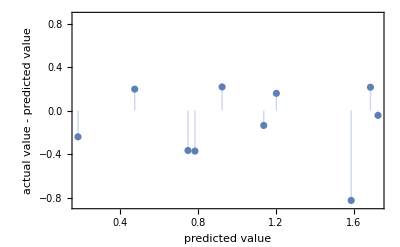
{-Graphics-,0.345482}

```mathematica
pm /@ {"ResidualPlot","StandardDeviation"}
```

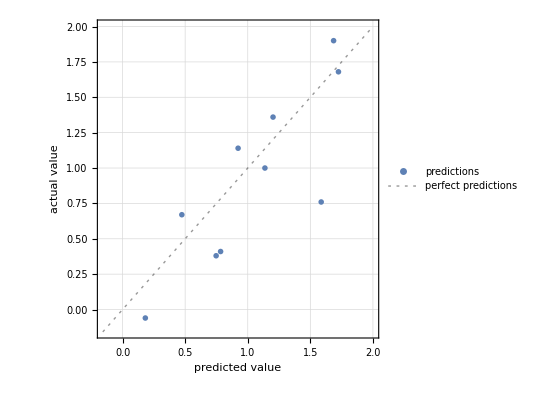

```mathematica
pm["ComparisonPlot"]
```

We looked for a pattern in least certain examples. They appear to correspond to ketals.

```mathematica
pm["LeastCertainExamples"]
```

{{0.949452,0.924307,0.906935,0.893135,0.69821,0.348736,0.501976,1.00424,0.990661,0.966102,0.946579,10.4605}→1.9,{1.11562,0.918295,0.909832,0.896179,0.703325,0.390259,0.482213,1.00849,1.18985,0.957627,0.917526,15.7488}→1.68,{1.15966,0.966662,0.968495,0.973115,1.04092,0.404933,1.07905,1.00849,1.13259,1.22881,1.10965,7.64651}→1.14,{1.11079,0.929499,0.918523,0.935238,1.17136,1.00968,1.39526,1.,1.13279,0.968927,0.969072,8.93488}→1.36,{0.998323,0.929499,0.899511,0.883666,0.659847,0.469872,1.28854,1.01132,0.990457,1.28249,1.10122,7.90233}→1.,{1.15966,0.959147,0.956183,0.945891,0.800512,0.133313,1.11858,0.992928,1.13259,1.22881,1.10965,6.0186}→0.76,{0.894061,0.962836,0.949303,0.974806,1.33504,0.797065,1.49407,1.00849,0.924263,0.980226,0.958763,-5.88372}→0.67,{0.836977,0.985244,0.958356,0.947244,0.790281,0.592882,1.3004,1.00141,0.848328,1.35593,1.08997,7.93953}→0.41,{1.16617,0.977729,0.984067,0.985289,1.,0.920075,1.04743,1.00849,1.19918,0.988701,0.958763,8.26512}→0.38,{0.894052,0.996311,0.985696,0.989009,1.03581,1.14674,1.21739,1.01414,0.924263,0.980226,0.958763,2.02326}→-0.06}

## NeuralNetwork

```mathematica
network = NetChain[
{LinearLayer[20],
ElementwiseLayer["Sigmoid"],
LinearLayer[10],
LinearLayer[1]
},
"Input"->12,
"Output"->1
]
```

NetChain[<>]

```mathematica
trainedNetwork=NetTrain[network,Thread[trainingData->Transpose[{trainingResults}]],
ValidationSet->Thread[testData->Transpose[{testResults}]]]
```

NetChain[<>]

```mathematica
predictedTestResults=Map[trainedNetwork,testData]⟦All,1⟧
```

{1.39673,1.84221,0.999192,0.756605,0.970376,1.06924,0.381235,0.763089,0.784902,0.0402112}

StandardDeviation:

```mathematica
Sqrt@Mean[(predictedTestResults-testResults)^2]
```

0.337943

## With Structural Information

## Creating Data

```mathematica
structuraldata=Import["https://github.com/madsutherland/Project/blob/master/Molecular%20Structures%20Real/Descriptors%202.xlsx?raw=true","XLSX"];
```

```mathematica
Dimensions@structuraldata
```

{4}

```mathematica
structuraldata=structuraldata[[4,4;;49,4;;]]
```

(1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
1. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
1. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1.
0. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 1. | 0. | 0.
1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1.
1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
1. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 1. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
Dimensions@structuraldata
```

{46,16}

```mathematica
structuraldata=Drop[structuraldata,{43}]
```

(1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
1. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
1. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1.
0. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 1. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 1. | 0. | 0.
1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1.
1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
1. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 1. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
Dimensions@structuraldata
```

{45,16}

```mathematica
(*command to split observations randomly*)
```

```mathematica
trainingIndices=Sort@RandomSample[Range[45],35]
```

{1,2,3,4,6,7,9,10,11,12,13,14,17,18,19,21,22,23,24,25,26,27,29,30,32,33,34,35,38,39,40,41,42,43,45}

```mathematica
fullData=ArrayFlatten[{{inputfinal,structuraldata}}]
```

{{4.26288,1.00751,1.02879,0.933717,-0.409207,1.01218,0.181818,1.,1.29772,1.07062,1.24086,11.4186,1.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,1.,0.,0.},{1.56584,0.973494,0.982799,0.889077,-0.434783,0.623166,0.533597,1.00141,1.20883,1.20339,1.01218,11.4047,1.,0.,1.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,1.,0.,0.},{1.00484,0.919661,0.910556,0.896517,0.69821,0.385264,0.498024,1.00707,1.05705,0.957627,0.935333,12.9209,1.,0.,1.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.,0.,0.},{1.06023,0.918705,0.912004,0.895333,0.659847,0.400562,0.498024,1.00283,1.12345,0.957627,0.935333,15.3814,1.,0.,1.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.,0.,0.},{0.949452,0.924307,0.906935,0.893135,0.69821,0.348736,0.501976,1.00424,0.990661,0.966102,0.946579,10.4605,1.,0.,1.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.,0.,0.},{1.62123,0.988933,0.865472,0.856611,0.731458,0.779894,-0.592885,1.00707,1.27523,1.16384,1.00281,12.8419,1.,0.,1.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,1.,0.,0.},{4.46109,1.00751,1.02969,0.934562,-0.409207,1.02123,0.181818,1.00283,1.23133,1.11582,1.2821,9.9814,0.,1.,1.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,1.,0.,0.},{1.11562,0.918295,0.909832,0.896179,0.703325,0.390259,0.482213,1.00849,1.18985,0.957627,0.917526,15.7488,1.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,1.,0.,0.},{1.51045,0.972947,0.987326,0.895333,-0.404092,0.660318,-0.517787,1.,1.14244,1.21751,1.03093,8.94419,1.,0.,1.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,1.,0.,0.},{1.51044,0.955458,0.964512,0.885019,-0.237852,1.25414,-0.865613,1.00849,1.14244,1.24859,1.03093,8.10698,0.,1.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.,0.,1.,0.,0.},{1.0554,0.933188,0.923592,0.942847,1.21483,0.986263,1.37945,1.00849,1.06639,0.968927,0.982193,6.47442,1.,0.,1.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.},{0.949447,0.929362,0.909651,0.896348,0.710997,0.41305,0.494071,1.01273,0.990661,0.985876,0.948454,11.4837,0.,1.,1.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.,0.,0.},{1.56584,0.977729,0.965598,0.885357,-0.248082,1.27505,-0.869565,1.,1.20883,1.23164,1.02156,10.5674,0.,1.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.,0.,1.,0.,0.},{0.894055,1.14128,0.931016,0.921711,0.790281,0.505151,0.525692,1.0099,0.924263,0.997175,0.961575,9.02326,0.,1.,1.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.,0.,0.},{1.15966,0.966662,0.968495,0.973115,1.04092,0.404933,1.07905,1.00849,1.13259,1.22881,1.10965,7.64651,1.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,1.,0.,0.},{1.11079,0.929499,0.918523,0.935238,1.17136,1.00968,1.39526,1.,1.13279,0.968927,0.969072,8.93488,1.,0.,1.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.},{1.45506,0.996311,0.981894,0.902097,-0.225064,1.36684,-0.881423,1.00141,1.07604,1.27119,1.04967,5.64651,0.,1.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.,0.,1.,0.,0.},{0.998319,0.992622,0.976462,0.993575,1.23529,0.480487,1.28854,1.,0.990457,1.28249,1.10122,7.90233,1.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.,0.},{1.11079,0.992622,0.996741,0.999493,1.03836,0.949422,1.04743,1.00849,1.13279,0.968927,0.969072,7.30698,1.,0.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.},{0.998323,0.929499,0.899511,0.883666,0.659847,0.469872,1.28854,1.01132,0.990457,1.28249,1.10122,7.90233,1.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.},{1.16618,0.944255,0.916712,0.934731,1.18926,1.02279,1.3913,1.00849,1.19918,0.966102,0.957826,11.3953,1.,0.,1.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.},{1.0554,0.992622,0.996741,0.998985,1.03069,0.964408,0.889328,1.0099,1.06639,0.99435,0.984067,5.86977,0.,1.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.},{1.21673,1.00751,1.03259,1.00795,0.657289,0.402123,1.06324,1.0099,1.20852,0.960452,1.00187,2.96279,1.,0.,1.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.},{1.11078,0.981418,0.985515,0.985966,0.994885,0.934749,1.04348,1.0099,1.13279,0.991525,0.970947,-8.56744,0.,1.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.},{1.51044,0.97404,0.995655,0.924586,-0.0767263,1.22385,1.1581,1.00707,1.14244,1.24859,1.03093,5.80465,0.,1.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,1.,0.},{1.51044,0.970351,1.00833,0.929828,-0.179028,1.15954,1.14229,1.00141,1.14244,1.24859,1.03093,-4.66512,0.,1.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,1.,0.},{1.45506,1.,1.00235,0.927968,-0.12532,1.25164,1.1581,0.992928,1.07604,1.27119,1.04967,3.34419,0.,1.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,1.,0.},{1.15966,0.959147,0.956183,0.945891,0.800512,0.133313,1.11858,0.992928,1.13259,1.22881,1.10965,6.0186,1.,0.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.},{1.51044,0.962836,0.978997,0.901589,-0.191816,1.37996,-0.893281,0.997171,1.14244,1.24859,1.03093,8.10698,0.,1.,0.,0.,1.,0.,0.,0.,0.,1.,0.,0.,0.,1.,0.,0.},{1.56584,0.959147,0.960167,0.88282,-0.209719,1.26225,-0.87747,1.00849,1.20883,1.23164,1.02156,10.5674,0.,1.,0.,0.,1.,0.,0.,0.,0.,1.,0.,0.,0.,1.,0.,0.},{0.894061,0.962836,0.949303,0.974806,1.33504,0.797065,1.49407,1.00849,0.924263,0.980226,0.958763,-5.88372,1.,0.,1.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.},{0.626755,1.06695,1.08112,1.07203,0.946292,0.489229,0.70751,1.,0.706402,0.99435,0.8791,10.4233,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.},{1.62122,0.959147,0.961615,0.883328,-0.225064,1.26975,-0.865613,1.00707,1.27523,1.21751,1.00281,13.0279,0.,1.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.,0.,1.,0.,0.},{1.38093,0.988933,1.01213,0.958573,0.202046,1.0537,1.05534,1.00707,1.4266,1.12429,1.02437,13.0698,1.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,1.,0.,1.,0.,0.},{0.998319,0.985244,0.964693,0.992898,1.3913,0.427412,1.04743,1.00849,0.990457,1.28249,1.10122,7.90233,1.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.},{0.836977,0.985244,0.958356,0.947244,0.790281,0.592882,1.3004,1.00141,0.848328,1.35593,1.08997,7.93953,1.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.,0.},{1.16617,0.977729,0.984067,0.985289,1.,0.920075,1.04743,1.00849,1.19918,0.988701,0.958763,8.26512,0.,1.,0.,1.,0.,0.,0.,0.,0.,0.,0.,1.,0.,1.,0.,0.},{1.56584,0.959147,0.950027,0.935577,0.731458,0.952232,1.18577,1.00566,1.20883,1.23164,1.02156,8.26512,0.,1.,0.,0.,0.,1.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.},{1.56584,0.977729,1.00181,0.924248,-0.171355,1.17109,1.12648,1.00424,1.20883,1.23164,1.02156,8.26512,0.,1.,0.,0.,1.,0.,0.,1.,0.,0.,0.,0.,0.,0.,1.,0.},{1.0554,1.,1.00018,0.999662,0.992327,0.979082,0.968379,1.01697,1.06639,0.968927,0.982193,4.84651,1.,0.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.},{1.11079,0.97404,0.97954,0.979709,0.982097,0.930066,1.02767,1.00849,1.13279,0.991525,0.970947,5.92093,0.,1.,0.,0.,1.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.},{1.05539,0.988933,0.992395,0.992898,0.997442,1.01062,0.98419,1.00849,1.06639,0.99435,0.984067,3.46047,0.,1.,0.,0.,1.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.},{0.999993,1.01872,1.03549,1.01573,0.736573,0.452388,1.20553,1.00424,1.,1.,1.,-14.3256,0.,1.,1.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.},{0.894052,0.996311,0.985696,0.989009,1.03581,1.14674,1.21739,1.01414,0.924263,0.980226,0.958763,2.02326,1.,0.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.},{0.838658,0.996311,0.985515,0.98884,1.03836,1.16266,1.21344,1.00849,0.85787,1.01695,0.975633,0.586047,0.,1.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
trainingData=fullData⟦trainingIndices⟧;
```

```mathematica
trainingResults=logMU⟦trainingIndices⟧;
```

```mathematica
testIndices=Complement[Range[45],trainingIndices]
```

{5,8,15,16,20,28,31,36,37,44}

```mathematica
testData=fullData⟦testIndices⟧
```

(0.949452 | 0.924307 | 0.906935 | 0.893135 | 0.69821 | 0.348736 | 0.501976 | 1.00424 | 0.990661 | 0.966102 | 0.946579 | 10.4605 | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0.
1.11562 | 0.918295 | 0.909832 | 0.896179 | 0.703325 | 0.390259 | 0.482213 | 1.00849 | 1.18985 | 0.957627 | 0.917526 | 15.7488 | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 1. | 0. | 0.
1.15966 | 0.966662 | 0.968495 | 0.973115 | 1.04092 | 0.404933 | 1.07905 | 1.00849 | 1.13259 | 1.22881 | 1.10965 | 7.64651 | 1. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0.
1.11079 | 0.929499 | 0.918523 | 0.935238 | 1.17136 | 1.00968 | 1.39526 | 1. | 1.13279 | 0.968927 | 0.969072 | 8.93488 | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0.998323 | 0.929499 | 0.899511 | 0.883666 | 0.659847 | 0.469872 | 1.28854 | 1.01132 | 0.990457 | 1.28249 | 1.10122 | 7.90233 | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1.
1.15966 | 0.959147 | 0.956183 | 0.945891 | 0.800512 | 0.133313 | 1.11858 | 0.992928 | 1.13259 | 1.22881 | 1.10965 | 6.0186 | 1. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1.
0.894061 | 0.962836 | 0.949303 | 0.974806 | 1.33504 | 0.797065 | 1.49407 | 1.00849 | 0.924263 | 0.980226 | 0.958763 | -5.88372 | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.836977 | 0.985244 | 0.958356 | 0.947244 | 0.790281 | 0.592882 | 1.3004 | 1.00141 | 0.848328 | 1.35593 | 1.08997 | 7.93953 | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
1.16617 | 0.977729 | 0.984067 | 0.985289 | 1. | 0.920075 | 1.04743 | 1.00849 | 1.19918 | 0.988701 | 0.958763 | 8.26512 | 0. | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 1. | 0. | 0.
0.894052 | 0.996311 | 0.985696 | 0.989009 | 1.03581 | 1.14674 | 1.21739 | 1.01414 | 0.924263 | 0.980226 | 0.958763 | 2.02326 | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
testResults=logMU⟦testIndices⟧
```

{1.9,1.68,1.14,1.36,1.,0.76,0.67,0.41,0.38,-0.06}

## Predict

```mathematica
p=Predict[Thread[trainingData->trainingResults],Method->"LinearRegression"]
```

PredictorFunction[…]

```mathematica
pm=PredictorMeasurements[p,Thread[testData->testResults]]
```

PredictorMeasurementsObject[…]

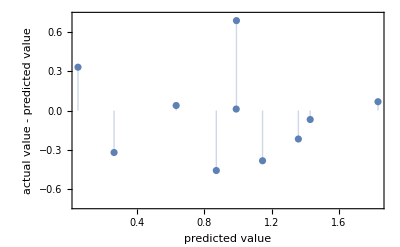
{-Graphics-,0.333065}

```mathematica
pm /@ {"ResidualPlot","StandardDeviation"}
```

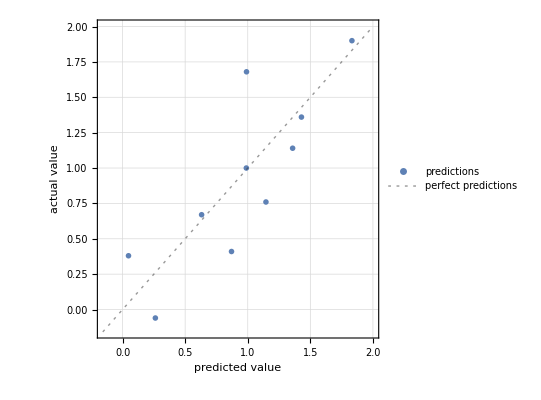

```mathematica
pm["ComparisonPlot"]
```

We looked for a pattern in least certain examples. They appear to correspond to ketals.

```mathematica
pm["LeastCertainExamples"]
```

{{0.949452,0.924307,0.906935,0.893135,0.69821,0.348736,0.501976,1.00424,0.990661,0.966102,0.946579,10.4605,1.,0.,1.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.,0.,0.}→1.9,{1.11562,0.918295,0.909832,0.896179,0.703325,0.390259,0.482213,1.00849,1.18985,0.957627,0.917526,15.7488,1.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,1.,0.,0.}→1.68,{1.15966,0.966662,0.968495,0.973115,1.04092,0.404933,1.07905,1.00849,1.13259,1.22881,1.10965,7.64651,1.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,1.,0.,0.}→1.14,{1.11079,0.929499,0.918523,0.935238,1.17136,1.00968,1.39526,1.,1.13279,0.968927,0.969072,8.93488,1.,0.,1.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.}→1.36,{0.998323,0.929499,0.899511,0.883666,0.659847,0.469872,1.28854,1.01132,0.990457,1.28249,1.10122,7.90233,1.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.}→1.,{1.15966,0.959147,0.956183,0.945891,0.800512,0.133313,1.11858,0.992928,1.13259,1.22881,1.10965,6.0186,1.,0.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.}→0.76,{0.894061,0.962836,0.949303,0.974806,1.33504,0.797065,1.49407,1.00849,0.924263,0.980226,0.958763,-5.88372,1.,0.,1.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.}→0.67,{0.836977,0.985244,0.958356,0.947244,0.790281,0.592882,1.3004,1.00141,0.848328,1.35593,1.08997,7.93953,1.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.,0.}→0.41,{1.16617,0.977729,0.984067,0.985289,1.,0.920075,1.04743,1.00849,1.19918,0.988701,0.958763,8.26512,0.,1.,0.,1.,0.,0.,0.,0.,0.,0.,0.,1.,0.,1.,0.,0.}→0.38,{0.894052,0.996311,0.985696,0.989009,1.03581,1.14674,1.21739,1.01414,0.924263,0.980226,0.958763,2.02326,1.,0.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.}→-0.06}

## NeuralNetwork

```mathematica
network = NetChain[
{LinearLayer[20],
ElementwiseLayer["SoftSign"],
LinearLayer[10],
LinearLayer[1]
},
"Input"->28,
"Output"->1
]
```

NetChain[<>]

```mathematica
trainedNetwork=NetTrain[network,Thread[trainingData->Transpose[{trainingResults}]],
ValidationSet->Thread[testData->Transpose[{testResults}]]]
```

NetChain[<>]

```mathematica
predictedTestResults=Map[trainedNetwork,testData]⟦All,1⟧
```

{1.66782,1.07719,1.39523,1.30395,1.10548,0.830269,0.589708,0.760869,0.388685,0.080749}

```mathematica
testResults
```

{1.9,1.68,1.14,1.36,1.,0.76,0.67,0.41,0.38,-0.06}

StandardDeviation:

```mathematica
Sqrt@Mean[(predictedTestResults-testResults)^2]
```

0.255161